# Analyzing Mathematica functions

## Creating functions to make word clouds

Get the names of every function and symbol:

```mathematica
names=CanonicalName/@WolframLanguageData[]
```

{$Aborted,$ActivationKey,$AllowDataUpdates,$AllowExternalChannelFunctions,$AllowInternet,$AssertFunction,$Assumptions,$AudioDecoders,$AudioEncoders,$AudioInputDevices,$AudioOutputDevices,$BaseDirectory,$BasePacletsDirectory,$BatchInput,$BatchOutput,$BlockchainBase,$ByteOrdering,$CacheBaseDirectory,$Canceled,$ChannelBase,$CharacterEncoding,$CharacterEncodings,$CloudAccountName,$CloudBase,$CloudConnected,$CloudCreditsAvailable,$CloudEvaluation,$CloudExpressionBase,$CloudObjectNameFormat,$CloudObjectURLType,$CloudRootDirectory,$CloudSymbolBase,$CloudUserID,$CloudUserUUID,$CloudVersion,$CommandLine,$CompilationTarget,$CompilerEnvironment,$Context,$ContextAliases,$ContextPath,$ControlActiveSetting,$CookieStore,$Cookies,$CreationDate,$CryptographicEllipticCurveNames,$CurrentLink,$CurrentTask,$CurrentWebSession,$DataStructures,$DateStringFormat,$DefaultAudioInputDevice,$DefaultAudioOutputDevice,$DefaultFrontEnd,$DefaultImagingDevice,$DefaultKernels,$DefaultLocalBase,$DefaultNetworkInterface,$DefaultProxyRules,$DefaultRemoteBatchSubmissionEnvironment,$DefaultRemoteKernel,$DefaultSystemCredentialStore,$Display,$DisplayFunction,$DistributedContexts,$DynamicEvaluation,$Echo,$EmbedCodeEnvironments,$EmbeddableServices,$Epilog,$EvaluationCloudBase,$EvaluationCloudObject,$EvaluationEnvironment,$ExportFormats,$ExternalIdentifierTypes,$ExternalStorageBase,$Failed,$FontFamilies,$FrontEnd,$FrontEndSession,$GeneratedAssetLocation,$GeoLocation,$GeoLocationCity,$GeoLocationCountry,$GeoLocationSource,$HistoryLength,$HomeDirectory,$IgnoreEOF,$ImageFormattingWidth,$ImageResolution,$ImagingDevice,$ImagingDevices,$ImportFormats,$IncomingMailSettings,$InitialDirectory,$Initialization,$InitializationContexts,$Input,$InputFileName,$InputStreamMethods,$Inspector,$InstallationDirectory,$InterpreterTypes,$IterationLimit,$KernelCount,$KernelID,$Language,$LibraryPath,$LicenseExpirationDate,$LicenseID,$LicenseServer,$Line,$Linked,$LocalBase,$LocalSymbolBase,$MachineAddresses,$MachineDomains,$MachineEpsilon,$MachineID,$MachineName,$MachinePrecision,$MachineType,$MaxExtraPrecision,$MaxMachineNumber,$MaxNumber,$MaxPiecewiseCases,$MaxPrecision,$MaxRootDegree,$MessageGroups,$MessageList,$MessagePrePrint,$Messages,$MinMachineNumber,$MinNumber,$MinPrecision,$MobilePhone,$ModuleNumber,$NetworkConnected,$NetworkInterfaces,$NewMessage,$NewSymbol,$NoValue,$NotebookInlineStorageLimit,$Notebooks,$NumberMarks,$OperatingSystem,$Output,$OutputSizeLimit,$OutputStreamMethods,$Packages,$ParentLink,$ParentProcessID,$PasswordFile,$Path,$PathnameSeparator,$PerformanceGoal,$Permissions,$PersistenceBase,$PersistencePath,$PlotTheme,$Post,$Pre,$PreInitialization,$PrePrint,$PreRead,$Printout3DPreviewer,$ProcessID,$ProcessorCount,$ProcessorType,$ProgressReporting,$PublisherID,$RandomGeneratorState,$RecursionLimit,$ReleaseNumber,$RequesterAddress,$RequesterCloudUserID,$RequesterCloudUserUUID,$RequesterWolframID,$RequesterWolframUUID,$ResourceSystemBase,$ResourceSystemPath,$RootDirectory,$SSHAuthentication,$ScriptCommandLine,$ScriptInputString,$ServiceCreditsAvailable,$Services,$SessionID,$SharedFunctions,$SharedVariables,$SoundDisplayFunction,$SourceLink,$SubtitleDecoders,$SubtitleEncoders,$SynchronousEvaluation,$SyntaxHandler,$System,$SystemCharacterEncoding,$SystemCredentialStore,$SystemID,$SystemShell,$SystemTimeZone,$SystemWordLength,$TargetSystems,$TemplatePath,$TemporaryDirectory,$TestFileName,$TimeUnit,$TimeZone,$TimeZoneEntity,$TimedOut,$UnitSystem,$Urgent,$UserAgentString,$UserBaseDirectory,$UserBasePacletsDirectory,$UserDocumentsDirectory,$UserURLBase,$Username,$Version,$VersionNumber,$VideoDecoders,$VideoEncoders,$VoiceStyles,$WolframDocumentsDirectory,$WolframID,$WolframUUID,AASTriangle,APIFunction,ARCHProcess,ARIMAProcess,ARMAProcess,ARProcess,ASATriangle,AbelianGroup,Abort,AbortKernels,AbortProtect,Above,Abs,AbsArg,AbsArgPlot,AbsoluteCorrelation,AbsoluteCorrelationFunction,AbsoluteCurrentValue,AbsoluteDashing,AbsoluteFileName,AbsoluteOptions,AbsolutePointSize,AbsoluteThickness,AbsoluteTime,AbsoluteTiming,AcceptanceThreshold,AccountingForm,Accumulate,Accuracy,AccuracyGoal,AcousticAbsorbingValue,AcousticImpedanceValue,AcousticNormalVelocityValue,AcousticPDEComponent,AcousticPressureCondition,AcousticRadiationValue,AcousticSoundHardValue,AcousticSoundSoftCondition,ActionMenu,Activate,ActiveClassification,ActiveClassificationObject,ActivePrediction,ActivePredictionObject,ActiveStyle,AcyclicGraphQ,AddSides,AddTo,AddToSearchIndex,AddUsers,AdjacencyGraph,AdjacencyList,AdjacencyMatrix,AdjacentMeshCells,Adjugate,AdjustTimeSeriesForecast,AdjustmentBox,AdjustmentBoxOptions,AdministrativeDivisionData,AffineHalfSpace,AffineSpace,AffineStateSpaceModel,AffineTransform,After,AggregatedEntityClass,AggregationLayer,AirPressureData,AirSoundAttenuation,AirTemperatureData,AircraftData,AirportData,AiryAi,AiryAiPrime,AiryAiZero,AiryBi,AiryBiPrime,AiryBiZero,AlgebraicIntegerQ,AlgebraicNumber,AlgebraicNumberDenominator,AlgebraicNumberNorm,AlgebraicNumberPolynomial,AlgebraicNumberTrace,AlgebraicUnitQ,Algebraics,Alignment,AlignmentPoint,All,AllTrue,AllowGroupClose,AllowInlineCells,AllowLooseGrammar,AllowReverseGroupClose,AllowVersionUpdate,AllowedCloudExtraParameters,AllowedCloudParameterExtensions,AllowedDimensions,AllowedFrequencyRange,AllowedHeads,AlphaChannel,Alphabet,AlphabeticOrder,AlphabeticSort,AlternatingFactorial,AlternatingGroup,AlternativeHypothesis,Alternatives,AltitudeMethod,AmbientLight,AmbiguityFunction,AmbiguityList,AnatomyData,AnatomyPlot3D,AnatomySkinStyle,AnatomyStyling,AnchoredSearch,And,AndersonDarlingTest,AngerJ,AngleBisector,AngleBracket,AnglePath,AnglePath3D,AngleVector,AngularGauge,Animate,AnimatedImage,AnimationDirection,AnimationRate,AnimationRepetitions,AnimationRunTime,AnimationRunning,AnimationTimeIndex,AnimationVideo,Animator,Annotate,Annotation,AnnotationDelete,AnnotationKeys,AnnotationRules,AnnotationValue,Annuity,AnnuityDue,Annulus,AnomalyDetection,AnomalyDetector,AnomalyDetectorFunction,Anonymous,Antialiasing,Antihermitian,AntihermitianMatrixQ,Antisymmetric,AntisymmetricMatrixQ,Antonyms,AnyOrder,AnySubset,AnyTrue,Apart,ApartSquareFree,Appearance,AppearanceElements,AppearanceRules,AppellF1,Append,AppendLayer,AppendTo,Application,Apply,ApplySides,ApplyTo,ArcCos,ArcCosh,ArcCot,ArcCoth,ArcCsc,ArcCsch,ArcCurvature,ArcLength,ArcSec,ArcSech,ArcSin,ArcSinDistribution,ArcSinh,ArcTan,ArcTanh,Area,Arg,ArgMax,ArgMin,ArgumentsOptions,ArithmeticGeometricMean,Around,AroundReplace,Array,ArrayComponents,ArrayDepth,ArrayFilter,ArrayFlatten,ArrayMesh,ArrayPad,ArrayPlot,ArrayPlot3D,ArrayQ,ArrayReduce,ArrayResample,ArrayReshape,ArrayRules,Arrays,Arrow,Arrowheads,Ask,AskAppend,AskConfirm,AskDisplay,AskFunction,AskState,AskTemplateDisplay,AskedQ,AskedValue,AspectRatio,Assert,AssessmentFunction,AssessmentResultObject,AssociateTo,Association,AssociationFormat,AssociationMap,AssociationQ,AssociationThread,AssumeDeterministic,Assuming,Assumptions,Asymptotic,AsymptoticDSolveValue,AsymptoticEqual,AsymptoticEquivalent,AsymptoticExpectation,AsymptoticGreater,AsymptoticGreaterEqual,AsymptoticIntegrate,AsymptoticLess,AsymptoticLessEqual,AsymptoticOutputTracker,AsymptoticProbability,AsymptoticProduct,AsymptoticRSolveValue,AsymptoticSolve,AsymptoticSum,Asynchronous,Atom,AtomCoordinates,AtomCount,AtomDiagramCoordinates,AtomLabelStyle,AtomLabels,AtomList,AtomQ,AttachCell,AttachedCell,AttentionLayer,Attributes,Audio,AudioAmplify,AudioAnnotate,AudioAnnotationLookup,AudioBlockMap,AudioCapture,AudioChannelAssignment,AudioChannelCombine,AudioChannelMix,AudioChannelSeparate,AudioChannels,AudioData,AudioDelay,AudioDelete,AudioDistance,AudioEncoding,AudioFade,AudioFrequencyShift,AudioGenerator,AudioIdentify,AudioInputDevice,AudioInsert,AudioInstanceQ,AudioIntervals,AudioJoin,AudioLabel,AudioLength,AudioLocalMeasurements,AudioLoudness,AudioMeasurements,AudioNormalize,AudioOutputDevice,AudioOverlay,AudioPad,AudioPan,AudioPartition,AudioPause,AudioPitchShift,AudioPlay,AudioPlot,AudioQ,AudioRecord,AudioReplace,AudioResample,AudioReverb,AudioReverse,AudioSampleRate,AudioSpectralMap,AudioSpectralTransformation,AudioSplit,AudioStop,AudioStream,AudioStreams,AudioTimeStretch,AudioTrackApply,AudioTrackSelection,AudioTrim,AudioType,AugmentedPolyhedron,AugmentedSymmetricPolynomial,Authentication,AuthenticationDialog,AutoAction,AutoCopy,AutoDelete,AutoIndent,AutoItalicWords,AutoMultiplicationSymbol,AutoOperatorRenderings,AutoRefreshed,AutoRemove,AutoScroll,AutoSpacing,AutoSubmitting,Autocomplete,AutocompletionFunction,AutocorrelationTest,Automatic,AutorunSequencing,Axes,AxesEdge,AxesLabel,AxesOrigin,AxesStyle,AxiomaticTheory,Axis,AxisLabel,AxisObject,AxisStyle,BSplineBasis,BSplineCurve,BSplineFunction,BSplineSurface,BabyMonsterGroupB,Back,Background,Backslash,Backward,Ball,Band,BandpassFilter,BandstopFilter,BarChart,BarChart3D,BarLegend,BarOrigin,BarSpacing,BarabasiAlbertGraphDistribution,BarcodeImage,BarcodeRecognize,BaringhausHenzeTest,BarlowProschanImportance,BarnesG,BartlettHannWindow,BartlettWindow,BaseDecode,BaseEncode,BaseForm,BaseStyle,Baseline,BaselinePosition,BasicRecurrentLayer,BatchNormalizationLayer,BatchSize,BatesDistribution,BattleLemarieWavelet,BayesianMaximization,BayesianMaximizationObject,BayesianMinimization,BayesianMinimizationObject,Because,BeckmannDistribution,Beep,Before,Begin,BeginDialogPacket,BeginPackage,BellB,BellY,Below,BenfordDistribution,BeniniDistribution,BenktanderGibratDistribution,BenktanderWeibullDistribution,BernoulliB,BernoulliDistribution,BernoulliGraphDistribution,BernoulliProcess,BernsteinBasis,BesagL,BesselFilterModel,BesselI,BesselJ,BesselJZero,BesselK,BesselY,BesselYZero,Beta,BetaBinomialDistribution,BetaDistribution,BetaNegativeBinomialDistribution,BetaPrimeDistribution,BetaRegularized,Between,BetweennessCentrality,BeveledPolyhedron,BezierCurve,BezierFunction,BilateralFilter,BilateralLaplaceTransform,BilateralZTransform,BinCounts,BinLists,Binarize,BinaryDeserialize,BinaryDistance,BinaryFormat,BinaryImageQ,BinaryRead,BinaryReadList,BinarySerialize,BinaryWrite,BinnedVariogramList,Binomial,BinomialDistribution,BinomialPointProcess,BinomialProcess,BinormalDistribution,BioSequence,BioSequenceBackTranslateList,BioSequenceComplement,BioSequenceInstances,BioSequenceModify,BioSequencePlot,BioSequenceQ,BioSequenceReverseComplement,BioSequenceTranscribe,BioSequenceTranslate,BiorthogonalSplineWavelet,BipartiteGraphQ,BiquadraticFilterModel,BirnbaumImportance,BirnbaumSaundersDistribution,BitAnd,BitClear,BitGet,BitLength,BitNot,BitOr,BitRate,BitSet,BitShiftLeft,BitShiftRight,BitXor,BiweightLocation,BiweightMidvariance,Black,BlackmanHarrisWindow,BlackmanNuttallWindow,BlackmanWindow,Blank,BlankNullSequence,BlankSequence,Blend,Block,BlockMap,BlockRandom,BlockchainAddressData,BlockchainBase,BlockchainBlockData,BlockchainContractValue,BlockchainData,BlockchainGet,BlockchainKeyEncode,BlockchainPut,BlockchainTokenData,BlockchainTransaction,BlockchainTransactionData,BlockchainTransactionSign,BlockchainTransactionSubmit,BlomqvistBeta,BlomqvistBetaTest,Blue,Blur,BodePlot,BohmanWindow,Bold,Bond,BondCount,BondLabelStyle,BondLabels,BondList,BondQ,Bookmarks,Boole,BooleanConsecutiveFunction,BooleanConvert,BooleanCountingFunction,BooleanFunction,BooleanGraph,BooleanMaxterms,BooleanMinimize,BooleanMinterms,BooleanQ,BooleanRegion,BooleanStrings,BooleanTable,BooleanVariables,Booleans,BorderDimensions,BorelTannerDistribution,Bottom,BottomHatTransform,BoundaryDiscretizeGraphics,BoundaryDiscretizeRegion,BoundaryMesh,BoundaryMeshRegion,BoundaryMeshRegionQ,BoundaryStyle,BoundedRegionQ,BoundingRegion,BoxData,BoxMatrix,BoxObject,BoxRatios,BoxStyle,BoxWhiskerChart,Boxed,Boxes,BracketingBar,BrayCurtisDistance,BreadthFirstScan,Break,BridgeData,BrightnessEqualize,BroadcastStationData,Brown,BrownForsytheTest,BrownianBridgeProcess,BubbleChart,BubbleChart3D,BubbleScale,BubbleSizes,BuildingData,BulletGauge,BusinessDayQ,ButterflyGraph,ButterworthFilterModel,Button,ButtonBar,ButtonBox,ButtonBoxOptions,ButtonData,ButtonFunction,ButtonMinHeight,ButtonNotebook,ButtonSource,Byte,ByteArray,ByteArrayFormat,ByteArrayFormatQ,ByteArrayQ,ByteArrayToString,ByteCount,ByteOrdering,C,CDF,CDFDeploy,CDFWavelet,CForm,CMYKColor,CSGRegion,CSGRegionQ,CSGRegionTree,CTCLossLayer,CachePersistence,CalendarConvert,CalendarData,CalendarType,CallPacket,Callout,CalloutMarker,CalloutStyle,CanberraDistance,Cancel,CancelButton,CandlestickChart,CanonicalGraph,CanonicalName,CanonicalWarpingCorrespondence,CanonicalWarpingDistance,CanonicalizePolygon,CanonicalizePolyhedron,CanonicalizeRegion,CantorMesh,CantorStaircase,Canvas,Cap,CapForm,CapitalDifferentialD,Capitalize,CapsuleShape,CaptureRunning,CarlemanLinearize,CarlsonRC,CarlsonRD,CarlsonRE,CarlsonRF,CarlsonRG,CarlsonRJ,CarlsonRK,CarlsonRM,CarmichaelLambda,CaseOrdering,CaseSensitive,Cases,Cashflow,Casoratian,Catalan,CatalanNumber,Catch,CategoricalDistribution,Catenate,CatenateLayer,CauchyDistribution,CauchyPointProcess,CauchyWindow,CayleyGraph,Ceiling,CelestialSystem,Cell,CellAutoOverwrite,CellBaseline,CellBracketOptions,CellChangeTimes,CellContext,CellDingbat,CellDynamicExpression,CellEditDuplicate,CellEpilog,CellEvaluationDuplicate,CellEvaluationFunction,CellEventActions,CellFrame,CellFrameColor,CellFrameLabelMargins,CellFrameLabels,CellFrameMargins,CellGroup,CellGroupData,CellGrouping,CellID,CellLabel,CellLabelAutoDelete,CellLabelStyle,CellMargins,CellObject,CellOpen,CellPrint,CellProlog,CellStyle,CellTags,Cells,CellularAutomaton,CensoredDistribution,Censoring,Center,CenterArray,CenterDot,CenteredInterval,CentralFeature,CentralMoment,CentralMomentGeneratingFunction,Cepstrogram,CepstrogramArray,CepstrumArray,ChampernowneNumber,ChanVeseBinarize,ChannelBase,ChannelBrokerAction,ChannelHistoryLength,ChannelListen,ChannelListener,ChannelListeners,ChannelObject,ChannelReceiverFunction,ChannelSend,ChannelSubscribers,Character,CharacterCounts,CharacterEncoding,CharacterName,CharacterNormalize,CharacterRange,CharacteristicFunction,CharacteristicPolynomial,Characters,ChartBaseStyle,ChartElementFunction,ChartElements,ChartLabels,ChartLayout,ChartLegends,ChartStyle,Chebyshev1FilterModel,Chebyshev2FilterModel,ChebyshevT,ChebyshevU,Check,CheckAbort,CheckArguments,Checkbox,CheckboxBar,ChemicalData,ChemicalFormula,ChemicalReaction,ChessboardDistance,ChiDistribution,ChiSquareDistribution,ChineseRemainder,ChoiceButtons,ChoiceDialog,CholeskyDecomposition,Chop,ChromaticPolynomial,ChromaticityPlot,ChromaticityPlot3D,Circle,CircleDot,CircleMinus,CirclePlus,CirclePoints,CircleThrough,CircleTimes,CirculantGraph,CircularOrthogonalMatrixDistribution,CircularQuaternionMatrixDistribution,CircularRealMatrixDistribution,CircularSymplecticMatrixDistribution,CircularUnitaryMatrixDistribution,Circumsphere,CityData,ClassPriors,ClassifierFunction,ClassifierMeasurements,ClassifierMeasurementsObject,Classify,Clear,ClearAll,ClearAttributes,ClearCookies,ClearPermissions,ClearSystemCache,ClebschGordan,ClickPane,ClickToCopy,ClickToCopyEnabled,Clip,ClipPlanes,ClipPlanesStyle,ClipRange,ClippingStyle,Clock,ClockGauge,Close,CloseKernels,ClosenessCentrality,Closing,CloudAccountData,CloudBase,CloudConnect,CloudDeploy,CloudDirectory,CloudDisconnect,CloudEvaluate,CloudExport,CloudExpression,CloudExpressions,CloudFunction,CloudGet,CloudImport,CloudLoggingData,CloudObject,CloudObjectNameFormat,CloudObjectURLType,CloudObjects,CloudPublish,CloudPut,CloudRenderingMethod,CloudSave,CloudShare,CloudSubmit,CloudSymbol,CloudUnshare,ClusterClassify,ClusterDissimilarityFunction,ClusteringComponents,ClusteringTree,CodeAssistOptions,Coefficient,CoefficientArrays,CoefficientList,CoefficientRules,CoifletWavelet,Collect,CollinearPoints,Colon,ColorBalance,ColorCombine,ColorConvert,ColorCoverage,ColorData,ColorDataFunction,ColorDetect,ColorDistance,ColorFunction,ColorFunctionBinning,ColorFunctionScaling,ColorNegate,ColorProfileData,ColorQ,ColorQuantize,ColorReplace,ColorRules,ColorSeparate,ColorSetter,ColorSlider,ColorSpace,ColorToneMapping,Colorize,ColorsNear,Column,ColumnAlignments,ColumnLines,ColumnSpacings,ColumnWidths,ColumnsEqual,CombinatorB,CombinatorC,CombinatorI,CombinatorK,CombinatorS,CombinatorW,CombinatorY,CombinedEntityClass,CombinerFunction,CometData,CommonName,CommonUnits,Commonest,CommonestFilter,CommunityBoundaryStyle,CommunityGraphPlot,CommunityLabels,CommunityRegionStyle,CompanyData,CompatibleUnitQ,CompilationOptions,CompilationTarget,Compile,Compiled,CompiledCodeFunction,CompiledFunction,CompiledLayer,CompilerEnvironment,CompilerEnvironmentAppendTo,CompilerEnvironmentObject,CompilerOptions,Complement,ComplementedEntityClass,CompleteGraph,CompleteGraphQ,CompleteIntegral,CompleteKaryTree,Complex,ComplexArrayPlot,ComplexContourPlot,ComplexExpand,ComplexInfinity,ComplexListPlot,ComplexPlot,ComplexPlot3D,ComplexRegionPlot,ComplexStreamPlot,ComplexVectorPlot,Complexes,ComplexityFunction,ComponentMeasurements,ComposeList,ComposeSeries,CompositeQ,Composition,CompoundElement,CompoundExpression,CompoundPoissonDistribution,CompoundPoissonProcess,CompoundRenewalProcess,Compress,CompressionLevel,ComputeUncertainty,ConcaveHullMesh,Condition,ConditionalExpression,Conditioned,Cone,ConfidenceLevel,ConfidenceRange,ConfidenceTransform,Confirm,ConfirmAssert,ConfirmBy,ConfirmMatch,ConfirmQuiet,ConformAudio,ConformImages,ConformationMethod,Congruent,ConicGradientFilling,ConicHullRegion,ConicOptimization,Conjugate,ConjugateTranspose,Conjunction,ConnectLibraryCallbackFunction,ConnectSystemModelComponents,ConnectSystemModelController,ConnectedComponents,ConnectedGraphComponents,ConnectedGraphQ,ConnectedMeshComponents,ConnectedMoleculeComponents,ConnectedMoleculeQ,ConnectionSettings,ConnesWindow,ConoverTest,ConservativeConvectionPDETerm,Constant,ConstantArray,ConstantImage,ConstantRegionQ,Constants,ConstellationData,Construct,Containing,ContainsAll,ContainsAny,ContainsExactly,ContainsNone,ContainsOnly,ContentDetectorFunction,ContentFieldOptions,ContentLocationFunction,ContentObject,ContentPadding,ContentSelectable,ContentSize,Context,ContextToFileName,Contexts,Continue,ContinuedFraction,ContinuedFractionK,ContinuousAction,ContinuousMarkovProcess,ContinuousTask,ContinuousTimeModelQ,ContinuousWaveletData,ContinuousWaveletTransform,ContourDetect,ContourLabels,ContourPlot,ContourPlot3D,ContourShading,ContourStyle,Contours,ContraharmonicMean,ContrastiveLossLayer,Control,ControlActive,ControlPlacement,ControlType,ControllabilityGramian,ControllabilityMatrix,ControllableDecomposition,ControllableModelQ,ControllerInformation,ControllerLinking,ControllerManipulate,ControllerMethod,ControllerPath,ControllerState,ControlsRendering,ConvectionPDETerm,Convergents,ConversionRules,ConvexHullMesh,ConvexHullRegion,ConvexOptimization,ConvexPolygonQ,ConvexPolyhedronQ,ConvexRegionQ,ConvolutionLayer,Convolve,ConwayGroupCo1,ConwayGroupCo2,ConwayGroupCo3,CookieFunction,CoordinateBoundingBox,CoordinateBoundingBoxArray,CoordinateBounds,CoordinateBoundsArray,CoordinateChartData,CoordinateTransform,CoordinateTransformData,CoordinatesToolOptions,CoplanarPoints,CoprimeQ,Coproduct,CopulaDistribution,CopyDatabin,CopyDirectory,CopyFile,CopyFunction,CopyToClipboard,Copyable,CoreNilpotentDecomposition,CornerFilter,CornerNeighbors,Correlation,CorrelationDistance,CorrelationFunction,CorrelationTest,Cos,CosIntegral,Cosh,CoshIntegral,CosineDistance,CosineWindow,Cot,Coth,CoulombF,CoulombG,CoulombH1,CoulombH2,Count,CountDistinct,CountDistinctBy,CountRoots,CountryData,Counts,CountsBy,Covariance,CovarianceEstimatorFunction,CovarianceFunction,CoxIngersollRossProcess,CoxModel,CoxModelFit,CoxianDistribution,CramerVonMisesTest,CreateArchive,CreateCellID,CreateChannel,CreateCloudExpression,CreateCompilerEnvironment,CreateDataStructure,CreateDataSystemModel,CreateDatabin,CreateDialog,CreateDirectory,CreateDocument,CreateFile,CreateIntermediateDirectories,CreateLicenseEntitlement,CreateManagedLibraryExpression,CreateNotebook,CreatePacletArchive,CreatePalette,CreatePermissionsGroup,CreateSearchIndex,CreateSystemModel,CreateUUID,CreateWindow,CriterionFunction,CriticalSection,CriticalityFailureImportance,CriticalitySuccessImportance,Cross,CrossEntropyLossLayer,CrossMatrix,CrossingCount,CrossingDetect,CrossingPolygon,Csc,Csch,Cube,CubeRoot,Cubics,Cuboid,Cumulant,CumulantGeneratingFunction,Cup,CupCap,Curl,CurrencyConvert,CurrentDate,CurrentImage,CurrentNotebookImage,CurrentScreenImage,CurrentValue,CurryApplied,CurvatureFlowFilter,CurveClosed,Cyan,CycleGraph,CycleIndexPolynomial,Cycles,CyclicGroup,Cyclotomic,Cylinder,CylindricalDecomposition,CylindricalDecompositionFunction,D,DEigensystem,DEigenvalues,DGaussianWavelet,DMSList,DMSString,DSolve,DSolveValue,DagumDistribution,DamData,DamerauLevenshteinDistance,Darker,Dashed,Dashing,DataDistribution,DataRange,DataReversed,DataStructure,DataStructureQ,DatabaseConnect,DatabaseDisconnect,DatabaseReference,Databin,DatabinAdd,DatabinSubmit,DatabinUpload,Databins,Dataset,DatasetTheme,DateBounds,DateDifference,DateFormat,DateFunction,DateHistogram,DateInterval,DateList,DateListLogPlot,DateListPlot,DateListStepPlot,DateObject,DateObjectQ,DateOverlapsQ,DatePattern,DatePlus,DateRange,DateReduction,DateScale,DateSelect,DateString,DateTicksFormat,DateValue,DateWithinQ,Dated,DatedUnit,DaubechiesWavelet,DavisDistribution,DawsonF,DayCount,DayCountConvention,DayHemisphere,DayMatchQ,DayName,DayNightTerminator,DayPlus,DayRange,DayRound,DaylightQ,DeBruijnGraph,DeBruijnSequence,Decapitalize,DecimalForm,DeclarePackage,Decompose,DeconvolutionLayer,Decrement,Decrypt,DecryptFile,DedekindEta,DeepSpaceProbeData,Default,DefaultAxesStyle,DefaultBaseStyle,DefaultBoxStyle,DefaultButton,DefaultDuplicateCellStyle,DefaultDuration,DefaultElement,DefaultFaceGridsStyle,DefaultFieldHintStyle,DefaultFrameStyle,DefaultFrameTicksStyle,DefaultGridLinesStyle,DefaultLabelStyle,DefaultMenuStyle,DefaultNaturalLanguage,DefaultNewCellStyle,DefaultOptions,DefaultPrintPrecision,DefaultTicksStyle,DefaultTooltipStyle,DefaultValues,Defer,DefineInputStreamMethod,DefineOutputStreamMethod,DefineResourceFunction,Definition,Degree,DegreeCentrality,DegreeGraphDistribution,Deinitialization,Del,DelaunayMesh,Delayed,Deletable,Delete,DeleteAnomalies,DeleteBorderComponents,DeleteCases,DeleteChannel,DeleteCloudExpression,DeleteContents,DeleteDirectory,DeleteDuplicates,DeleteDuplicatesBy,DeleteFile,DeleteMissing,DeleteObject,DeletePermissionsKey,DeleteSearchIndex,DeleteSmallComponents,DeleteStopwords,DelimitedSequence,Delimiter,DelimiterAutoMatching,DelimiterFlashTime,Delimiters,DeliveryFunction,Dendrogram,Denominator,DensityHistogram,DensityPlot,DensityPlot3D,DependentVariables,Deploy,Deployed,Depth,DepthFirstScan,Derivative,DerivativeFilter,DerivativePDETerm,DerivedKey,DescriptorStateSpace,DesignMatrix,Det,DeviceClose,DeviceConfigure,DeviceExecute,DeviceExecuteAsynchronous,DeviceObject,DeviceOpen,DeviceRead,DeviceReadBuffer,DeviceReadLatest,DeviceReadList,DeviceReadTimeSeries,DeviceStreams,DeviceWrite,DeviceWriteBuffer,Devices,Diagonal,DiagonalMatrix,DiagonalMatrixQ,DiagonalizableMatrixQ,Dialog,DialogInput,DialogNotebook,DialogProlog,DialogReturn,DialogSymbols,Diamond,DiamondMatrix,DiceDissimilarity,DictionaryLookup,DictionaryWordQ,DifferenceDelta,DifferenceQuotient,DifferenceRoot,DifferenceRootReduce,Differences,DifferentialD,DifferentialRoot,DifferentialRootReduce,DifferentiatorFilter,DiffusionPDETerm,DiggleGatesPointProcess,DiggleGrattonPointProcess,DigitBlock,DigitCharacter,DigitCount,DigitQ,DigitalSignature,DihedralAngle,DihedralGroup,Dilation,DimensionReduce,DimensionReducerFunction,DimensionReduction,DimensionalCombinations,DimensionalMeshComponents,Dimensions,DiracComb,DiracDelta,DirectedEdge,DirectedEdges,DirectedGraph,DirectedGraphQ,DirectedInfinity,Direction,DirectionalLight,Directive,Directory,DirectoryName,DirectoryQ,DirectoryStack,DirichletBeta,DirichletCharacter,DirichletCondition,DirichletConvolve,DirichletDistribution,DirichletEta,DirichletL,DirichletLambda,DirichletTransform,DirichletWindow,DisableFormatting,DiscreteAsymptotic,DiscreteChirpZTransform,DiscreteConvolve,DiscreteDelta,DiscreteHadamardTransform,DiscreteIndicator,DiscreteLQEstimatorGains,DiscreteLQRegulatorGains,DiscreteLimit,DiscreteLyapunovSolve,DiscreteMarkovProcess,DiscreteMaxLimit,DiscreteMinLimit,DiscretePlot,DiscretePlot3D,DiscreteRatio,DiscreteRiccatiSolve,DiscreteShift,DiscreteTimeModelQ,DiscreteUniformDistribution,DiscreteVariables,DiscreteWaveletData,DiscreteWaveletPacketTransform,DiscreteWaveletTransform,DiscretizeGraphics,DiscretizeRegion,Discriminant,DisjointQ,Disjunction,Disk,DiskMatrix,DiskSegment,Dispatch,DispersionEstimatorFunction,DisplayAllSteps,DisplayEndPacket,DisplayForm,DisplayFunction,DisplayPacket,DistanceFunction,DistanceMatrix,DistanceTransform,Distribute,DistributeDefinitions,Distributed,DistributedContexts,DistributionChart,DistributionFitTest,DistributionParameterAssumptions,DistributionParameterQ,Dithering,Div,Divide,DivideBy,DivideSides,Dividers,Divisible,DivisorSigma,DivisorSum,Divisors,Do,DockedCells,DocumentGenerator,DocumentGeneratorInformation,DocumentGenerators,DocumentNotebook,DocumentWeightingRules,Dodecahedron,DominantColors,DominatorTreeGraph,DominatorVertexList,Dot,DotDashed,DotEqual,DotLayer,Dotted,DoubleBracketingBar,DoubleDownArrow,DoubleLeftArrow,DoubleLeftRightArrow,DoubleLeftTee,DoubleLongLeftArrow,DoubleLongLeftRightArrow,DoubleLongRightArrow,DoubleRightArrow,DoubleRightTee,DoubleUpArrow,DoubleUpDownArrow,DoubleVerticalBar,DownArrow,DownArrowBar,DownArrowUpArrow,DownLeftRightVector,DownLeftTeeVector,DownLeftVector,DownLeftVectorBar,DownRightTeeVector,DownRightVector,DownRightVectorBar,DownTee,DownTeeArrow,DownValues,Downsample,DrazinInverse,Drop,DropoutLayer,Dt,DualPlanarGraph,DualPolyhedron,DualSystemsModel,DumpSave,DuplicateFreeQ,Duration,Dynamic,DynamicEvaluationTimeout,DynamicGeoGraphics,DynamicImage,DynamicModule,DynamicModuleValues,DynamicSetting,DynamicUpdating,DynamicWrapper,E,EarthImpactData,EarthquakeData,EccentricityCentrality,Echo,EchoEvaluation,EchoFunction,EchoLabel,EchoTiming,EclipseType,EdgeAdd,EdgeBetweennessCentrality,EdgeCapacity,EdgeChromaticNumber,EdgeConnectivity,EdgeContract,EdgeCost,EdgeCount,EdgeCoverQ,EdgeCycleMatrix,EdgeDelete,EdgeDetect,EdgeForm,EdgeIndex,EdgeLabelStyle,EdgeLabels,EdgeList,EdgeQ,EdgeRules,EdgeShapeFunction,EdgeStyle,EdgeTaggedGraph,EdgeTaggedGraphQ,EdgeTags,EdgeTransitiveGraphQ,EdgeValueRange,EdgeValueSizes,EdgeWeight,EdgeWeightedGraphQ,EditDistance,Editable,EffectiveInterest,Eigensystem,Eigenvalues,EigenvectorCentrality,Eigenvectors,Element,ElementData,ElementwiseLayer,ElidedForms,Eliminate,Ellipsoid,EllipticE,EllipticExp,EllipticExpPrime,EllipticF,EllipticFilterModel,EllipticK,EllipticLog,EllipticNomeQ,EllipticPi,EllipticTheta,EllipticThetaPrime,EmbedCode,EmbeddedHTML,EmbeddedSQLEntityClass,EmbeddedSQLExpression,EmbeddedService,EmbeddingLayer,EmitSound,EmpiricalDistribution,EmptyGraphQ,EmptyRegion,EmptySpaceF,Enabled,Enclose,Encode,Encrypt,EncryptFile,EncryptedObject,End,EndDialogPacket,EndOfBuffer,EndOfFile,EndOfLine,EndOfString,EndPackage,EngineeringForm,EnterExpressionPacket,EnterTextPacket,Entity,EntityClass,EntityClassList,EntityCopies,EntityFunction,EntityGroup,EntityInstance,EntityList,EntityPrefetch,EntityProperties,EntityProperty,EntityPropertyClass,EntityRegister,EntityStore,EntityStores,EntityTypeName,EntityUnregister,EntityValue,Entropy,EntropyFilter,Environment,Epilog,EpilogFunction,Equal,EqualTilde,EqualTo,Equilibrium,EquirippleFilterKernel,Equivalent,Erf,Erfc,Erfi,ErlangB,ErlangC,ErlangDistribution,Erosion,ErrorBox,EscapeRadius,EstimatedBackground,EstimatedDistribution,EstimatedPointProcess,EstimatedProcess,EstimatedVariogramModel,EstimatorGains,EstimatorRegulator,EuclideanDistance,EulerAngles,EulerCharacteristic,EulerE,EulerGamma,EulerMatrix,EulerPhi,EulerianGraphQ,Evaluatable,Evaluate,EvaluatePacket,EvaluationBox,EvaluationCell,EvaluationData,EvaluationElements,EvaluationEnvironment,EvaluationMonitor,EvaluationNotebook,EvaluationObject,EvaluationPrivileges,Evaluator,EvaluatorNames,EvenQ,EventData,EventHandler,EventLabels,EventSeries,ExactBlackmanWindow,ExactNumberQ,ExampleData,Except,ExcludePods,ExcludedContexts,ExcludedForms,ExcludedLines,ExcludedPhysicalQuantities,Exclusions,ExclusionsStyle,Exists,Exit,ExoplanetData,Exp,ExpGammaDistribution,ExpIntegralE,ExpIntegralEi,ExpToTrig,Expand,ExpandAll,ExpandDenominator,ExpandFileName,ExpandNumerator,Expectation,ExpirationDate,Exponent,ExponentFunction,ExponentStep,ExponentialDistribution,ExponentialFamily,ExponentialGeneratingFunction,ExponentialMovingAverage,ExponentialPowerDistribution,Export,ExportByteArray,ExportForm,ExportString,Expression,ExpressionCell,ExpressionGraph,ExpressionTree,ExpressionUUID,ExtendedEntityClass,ExtendedGCD,Extension,ExtentElementFunction,ExtentMarkers,ExtentSize,ExternalBundle,ExternalEvaluate,ExternalFunction,ExternalIdentifier,ExternalObject,ExternalOptions,ExternalSessionObject,ExternalSessions,ExternalStorageBase,ExternalStorageDownload,ExternalStorageGet,ExternalStorageObject,ExternalStoragePut,ExternalStorageUpload,ExternalTypeSignature,ExternalValue,Extract,ExtractArchive,ExtractLayer,ExtractPacletArchive,ExtremeValueDistribution,FARIMAProcess,FRatioDistribution,FaceAlign,FaceForm,FaceGrids,FaceGridsStyle,FaceRecognize,FacialFeatures,Factor,FactorInteger,FactorList,FactorSquareFree,FactorSquareFreeList,FactorTerms,FactorTermsList,Factorial,Factorial2,FactorialMoment,FactorialMomentGeneratingFunction,FactorialPower,Failure,FailureAction,FailureDistribution,FailureQ,False,FareySequence,FeatureDistance,FeatureExtract,FeatureExtraction,FeatureExtractor,FeatureExtractorFunction,FeatureNames,FeatureNearest,FeatureSpacePlot,FeatureSpacePlot3D,FeatureTypes,FeedbackLinearize,FeedbackSector,FeedbackSectorStyle,FeedbackType,FetalGrowthData,Fibonacci,Fibonorial,FieldCompletionFunction,FieldHint,FieldHintStyle,FieldMasked,FieldSize,File,FileBaseName,FileByteCount,FileConvert,FileDate,FileExistsQ,FileExtension,FileFormat,FileFormatProperties,FileFormatQ,FileHash,FileNameDepth,FileNameDrop,FileNameForms,FileNameJoin,FileNameSetter,FileNameSplit,FileNameTake,FileNameToFormatList,FileNames,FilePrint,FileSize,FileSystemMap,FileSystemScan,FileTemplate,FileTemplateApply,FileType,FilledCurve,FilledTorus,Filling,FillingStyle,FillingTransform,FilterRules,FilteredEntityClass,FinancialBond,FinancialData,FinancialDerivative,FinancialIndicator,Find,FindAnomalies,FindArgMax,FindArgMin,FindChannels,FindClique,FindClusters,FindCookies,FindCurvePath,FindCycle,FindDevices,FindDistribution,FindDistributionParameters,FindDivisions,FindEdgeColoring,FindEdgeCover,FindEdgeCut,FindEdgeIndependentPaths,FindEquationalProof,FindEulerianCycle,FindExternalEvaluators,FindFaces,FindFile,FindFit,FindFormula,FindFundamentalCycles,FindGeneratingFunction,FindGeoLocation,FindGeometricConjectures,FindGeometricTransform,FindGraphCommunities,FindGraphIsomorphism,FindGraphPartition,FindHamiltonianCycle,FindHamiltonianPath,FindHiddenMarkovStates,FindImageText,FindIndependentEdgeSet,FindIndependentVertexSet,FindInstance,FindIntegerNullVector,FindIsomers,FindIsomorphicSubgraph,FindKClan,FindKClique,FindKClub,FindKPlex,FindLibrary,FindLinearRecurrence,FindList,FindMatchingColor,FindMaxValue,FindMaximum,FindMaximumCut,FindMaximumFlow,FindMeshDefects,FindMinValue,FindMinimum,FindMinimumCostFlow,FindMinimumCut,FindMoleculeSubstructure,FindPath,FindPeaks,FindPermutation,FindPlanarColoring,FindPointProcessParameters,FindPostmanTour,FindProcessParameters,FindRegionTransform,FindRepeat,FindRoot,FindSequenceFunction,FindSettings,FindShortestPath,FindShortestTour,FindSpanningTree,FindSubgraphIsomorphism,FindSystemModelEquilibrium,FindTextualAnswer,FindThreshold,FindTransientRepeat,FindVertexColoring,FindVertexCover,FindVertexCut,FindVertexIndependentPaths,FinishDynamic,FiniteAbelianGroupCount,FiniteGroupCount,FiniteGroupData,First,FirstCase,FirstPassageTimeDistribution,FirstPosition,FischerGroupFi22,FischerGroupFi23,FischerGroupFi24Prime,FisherHypergeometricDistribution,FisherRatioTest,FisherZDistribution,Fit,FitRegularization,FittedModel,FixedOrder,FixedPoint,FixedPointList,Flat,FlatTopWindow,Flatten,FlattenAt,FlattenLayer,FlightData,FlipView,Floor,FlowPolynomial,Fold,FoldList,FoldPair,FoldPairList,FoldWhile,FoldWhileList,FollowRedirects,FontColor,FontFamily,FontSize,FontSlant,FontSubstitutions,FontTracking,FontVariations,FontWeight,For,ForAll,ForceVersionInstall,FormBox,FormBoxOptions,FormControl,FormFunction,FormLayoutFunction,FormObject,FormPage,FormProtectionMethod,Format,FormatType,FormulaData,FormulaLookup,FortranForm,Forward,ForwardBackward,ForwardCloudCredentials,Fourier,FourierCoefficient,FourierCosCoefficient,FourierCosSeries,FourierCosTransform,FourierDCT,FourierDCTFilter,FourierDCTMatrix,FourierDST,FourierDSTMatrix,FourierMatrix,FourierParameters,FourierSequenceTransform,FourierSeries,FourierSinCoefficient,FourierSinSeries,FourierSinTransform,FourierTransform,FourierTrigSeries,FoxH,FoxHReduce,FractionBox,FractionBoxOptions,FractionalBrownianMotionProcess,FractionalGaussianNoiseProcess,FractionalPart,Frame,FrameBox,FrameBoxOptions,FrameLabel,FrameListVideo,FrameMargins,FrameRate,FrameStyle,FrameTicks,FrameTicksStyle,Framed,FrechetDistribution,FreeQ,FrenetSerretSystem,FrequencySamplingFilterKernel,FresnelC,FresnelF,FresnelG,FresnelS,Friday,FrobeniusNumber,FrobeniusSolve,FromAbsoluteTime,FromCharacterCode,FromCoefficientRules,FromContinuedFraction,FromDMS,FromDateString,FromDigits,FromEntity,FromJulianDate,FromLetterNumber,FromPolarCoordinates,FromRomanNumeral,FromSphericalCoordinates,FromUnixTime,Front,FrontEndDynamicExpression,FrontEndEventActions,FrontEndExecute,FrontEndToken,FrontEndTokenExecute,Full,FullDefinition,FullForm,FullGraphics,FullInformationOutputRegulator,FullRegion,FullSimplify,Function,FunctionAnalytic,FunctionBijective,FunctionCompile,FunctionCompileExport,FunctionCompileExportByteArray,FunctionCompileExportLibrary,FunctionCompileExportString,FunctionContinuous,FunctionConvexity,FunctionDeclaration,FunctionDiscontinuities,FunctionDomain,FunctionExpand,FunctionInjective,FunctionInterpolation,FunctionLayer,FunctionMeromorphic,FunctionMonotonicity,FunctionPeriod,FunctionPoles,FunctionRange,FunctionSign,FunctionSingularities,FunctionSpace,FunctionSurjective,FussellVeselyImportance,GARCHProcess,GCD,GaborFilter,GaborMatrix,GaborWavelet,GainMargins,GainPhaseMargins,GalaxyData,GalleryView,Gamma,GammaDistribution,GammaRegularized,GapPenalty,GatedRecurrentLayer,Gather,GatherBy,GaugeFaceElementFunction,GaugeFaceStyle,GaugeFrameElementFunction,GaugeFrameSize,GaugeFrameStyle,GaugeLabels,GaugeMarkers,GaugeStyle,GaussianFilter,GaussianIntegers,GaussianMatrix,GaussianOrthogonalMatrixDistribution,GaussianSymplecticMatrixDistribution,GaussianUnitaryMatrixDistribution,GaussianWindow,GegenbauerC,General,GeneralizedLinearModelFit,GenerateAsymmetricKeyPair,GenerateConditions,GenerateDerivedKey,GenerateDigitalSignature,GenerateDocument,GenerateFileSignature,GenerateHTTPResponse,GenerateSecuredAuthenticationKey,GenerateSymmetricKey,GeneratedAssetFormat,GeneratedAssetLocation,GeneratedCell,GeneratedDocumentBinding,GeneratedParameters,GeneratedQuantityMagnitudes,GeneratingFunction,GeneratorDescription,GeneratorHistoryLength,GeneratorOutputType,GenericCylindricalDecomposition,GenomeData,GenomeLookup,GeoAntipode,GeoArea,GeoArraySize,GeoBackground,GeoBoundary,GeoBoundingBox,GeoBounds,GeoBoundsRegion,GeoBoundsRegionBoundary,GeoBubbleChart,GeoCenter,GeoCircle,GeoContourPlot,GeoDensityPlot,GeoDestination,GeoDirection,GeoDisk,GeoDisplacement,GeoDistance,GeoDistanceList,GeoElevationData,GeoEntities,GeoGraphPlot,GeoGraphValuePlot,GeoGraphics,GeoGridDirectionDifference,GeoGridLines,GeoGridLinesStyle,GeoGridPosition,GeoGridRange,GeoGridRangePadding,GeoGridUnitArea,GeoGridUnitDistance,GeoGridVector,GeoGroup,GeoHemisphere,GeoHemisphereBoundary,GeoHistogram,GeoIdentify,GeoImage,GeoLabels,GeoLength,GeoListPlot,GeoLocation,GeoMarker,GeoModel,GeoNearest,GeoOrientationData,GeoPath,GeoPolygon,GeoPosition,GeoPositionENU,GeoPositionXYZ,GeoProjection,GeoProjectionData,GeoRange,GeoRangePadding,GeoRegionValuePlot,GeoResolution,GeoScaleBar,GeoServer,GeoSmoothHistogram,GeoStreamPlot,GeoStyling,GeoStylingImageFunction,GeoVariant,GeoVector,GeoVectorENU,GeoVectorPlot,GeoVectorXYZ,GeoVisibleRegion,GeoVisibleRegionBoundary,GeoWithinQ,GeoZoomLevel,GeodesicClosing,GeodesicDilation,GeodesicErosion,GeodesicOpening,GeodesyData,GeogravityModelData,GeologicalPeriodData,GeomagneticModelData,GeometricAssertion,GeometricBrownianMotionProcess,GeometricDistribution,GeometricMean,GeometricMeanFilter,GeometricOptimization,GeometricScene,GeometricStep,GeometricTest,GeometricTransformation,GestureHandler,Get,GetEnvironment,GibbsPointProcess,Glaisher,GlobalClusteringCoefficient,Glow,GoldenAngle,GoldenRatio,GompertzMakehamDistribution,GoochShading,GoodmanKruskalGamma,GoodmanKruskalGammaTest,Goto,Grad,Gradient,GradientFilter,GradientFittedMesh,GradientOrientationFilter,GrammarApply,GrammarRules,GrammarToken,Graph,Graph3D,GraphAssortativity,GraphAutomorphismGroup,GraphCenter,GraphComplement,GraphData,GraphDensity,GraphDiameter,GraphDifference,GraphDisjointUnion,GraphDistance,GraphDistanceMatrix,GraphEmbedding,GraphHighlight,GraphHighlightStyle,GraphHub,GraphIntersection,GraphLayerStyle,GraphLayers,GraphLayout,GraphLinkEfficiency,GraphPeriphery,GraphPlot,GraphPlot3D,GraphPower,GraphPropertyDistribution,GraphQ,GraphRadius,GraphReciprocity,GraphTree,GraphUnion,Graphics,Graphics3D,GraphicsColumn,GraphicsComplex,GraphicsGrid,GraphicsGroup,GraphicsRow,Gray,GrayLevel,Greater,GreaterEqual,GreaterEqualLess,GreaterEqualThan,GreaterFullEqual,GreaterGreater,GreaterLess,GreaterSlantEqual,GreaterThan,GreaterTilde,Green,GreenFunction,Grid,GridBox,GridDefaultElement,GridGraph,GridLines,GridLinesStyle,GridVideo,GroebnerBasis,GroupActionBase,GroupBy,GroupCentralizer,GroupElementFromWord,GroupElementPosition,GroupElementQ,GroupElementToWord,GroupElements,GroupGenerators,GroupMultiplicationTable,GroupOrbits,GroupOrder,GroupPageBreakWithin,GroupSetwiseStabilizer,GroupStabilizer,GroupStabilizerChain,Groupings,GrowCutComponents,Gudermannian,GuidedFilter,GumbelDistribution,HITSCentrality,HTTPErrorResponse,HTTPRedirect,HTTPRequest,HTTPRequestData,HTTPResponse,HaarWavelet,HadamardMatrix,HalfLine,HalfNormalDistribution,HalfPlane,HalfSpace,HalftoneShading,HamiltonianGraphQ,HammingDistance,HammingWindow,HandlerFunctions,HandlerFunctionsKeys,HankelH1,HankelH2,HankelMatrix,HankelTransform,HannPoissonWindow,HannWindow,HaradaNortonGroupHN,HararyGraph,HardcorePointProcess,HarmonicMean,HarmonicMeanFilter,HarmonicNumber,Hash,HatchFilling,HatchShading,Haversine,HazardFunction,Head,HeaderAlignment,HeaderBackground,HeaderDisplayFunction,HeaderLines,HeaderSize,HeaderStyle,Heads,HeatFluxValue,HeatInsulationValue,HeatOutflowValue,HeatRadiationValue,HeatSymmetryValue,HeatTemperatureCondition,HeatTransferPDEComponent,HeatTransferValue,HeavisideLambda,HeavisidePi,HeavisideTheta,HeldGroupHe,HelmholtzPDEComponent,Here,HermiteDecomposition,HermiteH,Hermitian,HermitianMatrixQ,HessenbergDecomposition,HeunB,HeunBPrime,HeunC,HeunCPrime,HeunD,HeunDPrime,HeunG,HeunGPrime,HeunT,HeunTPrime,HexadecimalCharacter,Hexahedron,HiddenItems,HiddenMarkovProcess,HighlightGraph,HighlightImage,HighlightMesh,Highlighted,HighpassFilter,HigmanSimsGroupHS,HilbertCurve,HilbertFilter,HilbertMatrix,Histogram,Histogram3D,HistogramDistribution,HistogramList,HistogramPointDensity,HistogramTransform,HistogramTransformInterpolation,HistoricalPeriodData,HitMissTransform,HjorthDistribution,HodgeDual,HoeffdingD,HoeffdingDTest,Hold,HoldAll,HoldAllComplete,HoldComplete,HoldFirst,HoldForm,HoldPattern,HoldRest,HolidayCalendar,HorizontalGauge,HornerForm,HostLookup,HotellingTSquareDistribution,HoytDistribution,Hue,HumanGrowthData,HumpDownHump,HumpEqual,HurwitzLerchPhi,HurwitzZeta,HyperbolicDistribution,HypercubeGraph,HyperexponentialDistribution,Hyperfactorial,Hypergeometric0F1,Hypergeometric0F1Regularized,Hypergeometric1F1,Hypergeometric1F1Regularized,Hypergeometric2F1,Hypergeometric2F1Regularized,HypergeometricDistribution,HypergeometricPFQ,HypergeometricPFQRegularized,HypergeometricU,Hyperlink,HyperlinkAction,Hyperplane,Hyphenation,HypoexponentialDistribution,HypothesisTestData,I,IPAddress,IconData,IconRules,Iconize,Icosahedron,Identity,IdentityMatrix,If,IgnoreCase,IgnoreDiacritics,IgnoreIsotopes,IgnorePunctuation,IgnoreStereochemistry,IgnoringInactive,Im,Image,Image3D,Image3DProjection,Image3DSlices,ImageAccumulate,ImageAdd,ImageAdjust,ImageAlign,ImageApply,ImageApplyIndexed,ImageAspectRatio,ImageAssemble,ImageAugmentationLayer,ImageBoundingBoxes,ImageCapture,ImageCaptureFunction,ImageCases,ImageChannels,ImageClip,ImageCollage,ImageColorSpace,ImageCompose,ImageContainsQ,ImageContents,ImageConvolve,ImageCooccurrence,ImageCorners,ImageCorrelate,ImageCorrespondingPoints,ImageCrop,ImageData,ImageDeconvolve,ImageDemosaic,ImageDifference,ImageDimensions,ImageDisplacements,ImageDistance,ImageEffect,ImageExposureCombine,ImageFeatureTrack,ImageFileApply,ImageFileFilter,ImageFileScan,ImageFilter,ImageFocusCombine,ImageForestingComponents,ImageFormattingWidth,ImageForwardTransformation,ImageGraphics,ImageHistogram,ImageIdentify,ImageInstanceQ,ImageKeypoints,ImageLabels,ImageLegends,ImageLevels,ImageLines,ImageMargins,ImageMarker,ImageMeasurements,ImageMesh,ImageMultiply,ImagePad,ImagePadding,ImagePartition,ImagePeriodogram,ImagePerspectiveTransformation,ImagePosition,ImagePreviewFunction,ImagePyramid,ImagePyramidApply,ImageQ,ImageRecolor,ImageReflect,ImageResize,ImageResolution,ImageRestyle,ImageRotate,ImageSaliencyFilter,ImageScaled,ImageScan,ImageSize,ImageSizeAction,ImageSizeMultipliers,ImageStitch,ImageSubtract,ImageTake,ImageTransformation,ImageTrim,ImageType,ImageValue,ImageValuePositions,ImageVectorscopePlot,ImageWaveformPlot,ImagingDevice,ImplicitRegion,Implies,Import,ImportByteArray,ImportOptions,ImportString,ImportedObject,ImprovementImportance,In,InString,Inactivate,Inactive,IncidenceGraph,IncidenceList,IncidenceMatrix,IncludeAromaticBonds,IncludeConstantBasis,IncludeDefinitions,IncludeDirectories,IncludeGeneratorTasks,IncludeHydrogens,IncludeInflections,IncludeMetaInformation,IncludePods,IncludeQuantities,IncludeRelatedTables,IncludeWindowTimes,IncludedContexts,Increment,IndefiniteMatrixQ,IndependenceTest,IndependentEdgeSetQ,IndependentPhysicalQuantity,IndependentUnit,IndependentUnitDimension,IndependentVertexSetQ,Indeterminate,IndeterminateThreshold,IndexEdgeTaggedGraph,IndexGraph,Indexed,InexactNumberQ,InfiniteFuture,InfiniteLine,InfinitePast,InfinitePlane,Infinity,Infix,InflationAdjust,InflationMethod,Information,InheritScope,Inherited,InhomogeneousPoissonPointProcess,InhomogeneousPoissonProcess,InitialEvaluationHistory,InitialSeeding,Initialization,InitializationCell,InitializationObject,InitializationObjects,InitializationValue,Initialize,Inner,InnerPolygon,InnerPolyhedron,Inpaint,Input,InputAliases,InputAssumptions,InputAutoReplacements,InputField,InputForm,InputNamePacket,InputNotebook,InputPacket,InputPorts,InputStream,InputString,InputStringPacket,Insert,InsertLinebreaks,InsertResults,InsertionFunction,Inset,Insphere,Install,InstallService,Integer,IntegerDigits,IntegerExponent,IntegerLength,IntegerName,IntegerPart,IntegerPartitions,IntegerQ,IntegerReverse,IntegerString,Integers,Integrate,Interactive,InteractiveTradingChart,InterfaceSwitched,Interleaving,InternallyBalancedDecomposition,InterpolatingFunction,InterpolatingPolynomial,Interpolation,InterpolationOrder,InterpolationPoints,Interpretation,InterpretationBox,InterpretationBoxOptions,InterpretationFunction,Interpreter,InterquartileRange,Interrupt,IntersectedEntityClass,IntersectingQ,Intersection,Interval,IntervalIntersection,IntervalMarkers,IntervalMarkersStyle,IntervalMemberQ,IntervalSlider,IntervalUnion,Inverse,InverseBetaRegularized,InverseBilateralLaplaceTransform,InverseBilateralZTransform,InverseCDF,InverseChiSquareDistribution,InverseContinuousWaveletTransform,InverseDistanceTransform,InverseEllipticNomeQ,InverseErf,InverseErfc,InverseFourier,InverseFourierCosTransform,InverseFourierSequenceTransform,InverseFourierSinTransform,InverseFourierTransform,InverseFunction,InverseFunctions,InverseGammaDistribution,InverseGammaRegularized,InverseGaussianDistribution,InverseGudermannian,InverseHankelTransform,InverseHaversine,InverseImagePyramid,InverseJacobiCD,InverseJacobiCN,InverseJacobiCS,InverseJacobiDC,InverseJacobiDN,InverseJacobiDS,InverseJacobiNC,InverseJacobiND,InverseJacobiNS,InverseJacobiSC,InverseJacobiSD,InverseJacobiSN,InverseLaplaceTransform,InverseMellinTransform,InversePermutation,InverseRadon,InverseRadonTransform,InverseSeries,InverseShortTimeFourier,InverseSpectrogram,InverseSurvivalFunction,InverseTransformedRegion,InverseWaveletTransform,InverseWeierstrassP,InverseWishartMatrixDistribution,InverseZTransform,Invisible,IrreduciblePolynomialQ,IslandData,IsolatingInterval,IsomorphicGraphQ,IsomorphicSubgraphQ,IsotopeData,Italic,Item,ItemAspectRatio,ItemDisplayFunction,ItemSize,ItemStyle,ItoProcess,JaccardDissimilarity,JacobiAmplitude,JacobiCD,JacobiCN,JacobiCS,JacobiDC,JacobiDN,JacobiDS,JacobiEpsilon,JacobiNC,JacobiND,JacobiNS,JacobiP,JacobiSC,JacobiSD,JacobiSN,JacobiSymbol,JacobiZN,JacobiZeta,JankoGroupJ1,JankoGroupJ2,JankoGroupJ3,JankoGroupJ4,JarqueBeraALMTest,JohnsonDistribution,Join,JoinAcross,JoinForm,Joined,JoinedCurve,JordanDecomposition,JordanModelDecomposition,JuliaSetBoettcher,JuliaSetIterationCount,JuliaSetPlot,JuliaSetPoints,JulianDate,KCoreComponents,KDistribution,KEdgeConnectedComponents,KEdgeConnectedGraphQ,KVertexConnectedComponents,KVertexConnectedGraphQ,KagiChart,KaiserBesselWindow,KaiserWindow,KalmanEstimator,KalmanFilter,KarhunenLoeveDecomposition,KaryTree,KatzCentrality,KeepExistingVersion,KelvinBei,KelvinBer,KelvinKei,KelvinKer,KendallTau,KendallTauTest,KernelFunction,KernelMixtureDistribution,KernelObject,Kernels,Key,KeyCollisionFunction,KeyComplement,KeyDrop,KeyDropFrom,KeyExistsQ,KeyFreeQ,KeyIntersection,KeyMap,KeyMemberQ,KeySelect,KeySort,KeySortBy,KeyTake,KeyUnion,KeyValueMap,KeyValuePattern,KeypointStrength,Keys,Khinchin,KillProcess,KirchhoffGraph,KirchhoffMatrix,KleinInvariantJ,KnapsackSolve,KnightTourGraph,KnotData,KnownUnitQ,KochCurve,KolmogorovSmirnovTest,KroneckerDelta,KroneckerModelDecomposition,KroneckerProduct,KroneckerSymbol,KuiperTest,KumaraswamyDistribution,Kurtosis,KuwaharaFilter,LABColor,LCHColor,LCM,LQEstimatorGains,LQGRegulator,LQOutputRegulatorGains,LQRegulatorGains,LUDecomposition,LUVColor,Label,LabelStyle,LabelVisibility,Labeled,LabelingFunction,LabelingSize,LaguerreL,LakeData,LambdaComponents,LameC,LameCPrime,LameEigenvalueA,LameEigenvalueB,LameS,LameSPrime,LaminaData,LanczosWindow,LandauDistribution,Language,LanguageCategory,LanguageData,LanguageIdentify,LaplaceDistribution,LaplaceTransform,Laplacian,LaplacianFilter,LaplacianGaussianFilter,LaplacianPDETerm,Large,Larger,Last,Latitude,LatitudeLongitude,LatticeData,LatticeReduce,LaunchKernels,LayerSizeFunction,LayeredGraphPlot,LayeredGraphPlot3D,LeaderSize,LeafCount,LeapVariant,LeapYearQ,LearnDistribution,LearnedDistribution,LearningRate,LearningRateMultipliers,LeastSquares,LeastSquaresFilterKernel,Left,LeftArrow,LeftArrowBar,LeftArrowRightArrow,LeftDownTeeVector,LeftDownVector,LeftDownVectorBar,LeftRightArrow,LeftRightVector,LeftTee,LeftTeeArrow,LeftTeeVector,LeftTriangle,LeftTriangleBar,LeftTriangleEqual,LeftUpDownVector,LeftUpTeeVector,LeftUpVector,LeftUpVectorBar,LeftVector,LeftVectorBar,LegendAppearance,LegendFunction,LegendLabel,LegendLayout,LegendMargins,LegendMarkerSize,LegendMarkers,Legended,LegendreP,LegendreQ,Length,LengthWhile,LerchPhi,Less,LessEqual,LessEqualGreater,LessEqualThan,LessFullEqual,LessGreater,LessLess,LessSlantEqual,LessThan,LessTilde,LetterCharacter,LetterCounts,LetterNumber,LetterQ,Level,LeveneTest,LeviCivitaTensor,LevyDistribution,LexicographicOrder,LexicographicSort,LibraryDataType,LibraryFunction,LibraryFunctionError,LibraryFunctionInformation,LibraryFunctionLoad,LibraryFunctionUnload,LibraryLoad,LibraryUnload,LicenseEntitlementObject,LicenseEntitlements,LicensingSettings,LiftingFilterData,LiftingWaveletTransform,LightBlue,LightBrown,LightCyan,LightGray,LightGreen,LightMagenta,LightOrange,LightPink,LightPurple,LightRed,LightYellow,Lighter,Lighting,LightingAngle,Likelihood,Limit,LimitsPositioning,LindleyDistribution,Line,LineBreakChart,LineGraph,LineIndent,LineIndentMaxFraction,LineIntegralConvolutionPlot,LineIntegralConvolutionScale,LineLegend,LineSpacing,LinearFractionalOptimization,LinearFractionalTransform,LinearGradientFilling,LinearGradientImage,LinearLayer,LinearModelFit,LinearOffsetFunction,LinearOptimization,LinearRecurrence,LinearSolve,LinearSolveFunction,LinearizingTransformationData,LinkActivate,LinkClose,LinkConnect,LinkCreate,LinkFunction,LinkInterrupt,LinkLaunch,LinkObject,LinkPatterns,LinkProtocol,LinkRankCentrality,LinkRead,LinkReadyQ,LinkWrite,Links,LiouvilleLambda,List,ListAnimate,ListContourPlot,ListContourPlot3D,ListConvolve,ListCorrelate,ListCurvePathPlot,ListDeconvolve,ListDensityPlot,ListDensityPlot3D,ListFormat,ListFourierSequenceTransform,ListInterpolation,ListLineIntegralConvolutionPlot,ListLinePlot,ListLinePlot3D,ListLogLinearPlot,ListLogLogPlot,ListLogPlot,ListPicker,ListPickerBox,ListPickerBoxOptions,ListPlay,ListPlot,ListPlot3D,ListPointPlot3D,ListPolarPlot,ListQ,ListSliceContourPlot3D,ListSliceDensityPlot3D,ListSliceVectorPlot3D,ListStepPlot,ListStreamDensityPlot,ListStreamPlot,ListStreamPlot3D,ListSurfacePlot3D,ListVectorDensityPlot,ListVectorDisplacementPlot,ListVectorDisplacementPlot3D,ListVectorPlot,ListVectorPlot3D,ListZTransform,Listable,LocalAdaptiveBinarize,LocalCache,LocalClusteringCoefficient,LocalObject,LocalObjects,LocalResponseNormalizationLayer,LocalSubmit,LocalSymbol,LocalTime,LocalTimeZone,LocalizeVariables,LocationEquivalenceTest,LocationTest,Locator,LocatorAutoCreate,LocatorPane,LocatorRegion,Locked,Log,Log10,Log2,LogBarnesG,LogGamma,LogGammaDistribution,LogIntegral,LogLikelihood,LogLinearPlot,LogLogPlot,LogLogisticDistribution,LogMultinormalDistribution,LogNormalDistribution,LogPlot,LogRankTest,LogSeriesDistribution,LogicalExpand,LogisticDistribution,LogisticSigmoid,LogitModelFit,LongLeftArrow,LongLeftRightArrow,LongRightArrow,LongShortTermMemoryLayer,Longest,LongestCommonSequence,LongestCommonSequencePositions,LongestCommonSubsequence,LongestCommonSubsequencePositions,LongestOrderedSequence,Longitude,Lookup,LoopFreeGraphQ,Looping,LossFunction,LowerCaseQ,LowerLeftArrow,LowerRightArrow,LowerTriangularMatrixQ,LowerTriangularize,LowpassFilter,LucasL,LuccioSamiComponents,LunarEclipse,LyapunovSolve,LyonsGroupLy,MAProcess,MIMETypeToFormatList,MachineNumberQ,MachinePrecision,Magenta,Magnification,Magnify,MailAddressValidation,MailExecute,MailFolder,MailItem,MailReceiverFunction,MailResponseFunction,MailSearch,MailServerConnect,MailServerConnection,MailSettings,Majority,MakeBoxes,MakeExpression,ManagedLibraryExpressionID,ManagedLibraryExpressionQ,MandelbrotSetBoettcher,MandelbrotSetDistance,MandelbrotSetIterationCount,MandelbrotSetMemberQ,MandelbrotSetPlot,MangoldtLambda,ManhattanDistance,Manipulate,Manipulator,MannWhitneyTest,MannedSpaceMissionData,MantissaExponent,Manual,Map,MapAll,MapAt,MapIndexed,MapThread,MarchenkoPasturDistribution,MarcumQ,MardiaCombinedTest,MardiaKurtosisTest,MardiaSkewnessTest,MarginalDistribution,MarkovProcessProperties,Masking,MassConcentrationCondition,MassFluxValue,MassImpermeableBoundaryValue,MassOutflowValue,MassSymmetryValue,MassTransferValue,MassTransportPDEComponent,MatchLocalNames,MatchQ,MatchingDissimilarity,MaterialShading,MaternPointProcess,MathMLForm,MathematicalFunctionData,MathieuC,MathieuCPrime,MathieuCharacteristicA,MathieuCharacteristicB,MathieuCharacteristicExponent,MathieuGroupM11,MathieuGroupM12,MathieuGroupM22,MathieuGroupM23,MathieuGroupM24,MathieuS,MathieuSPrime,Matrices,MatrixExp,MatrixForm,MatrixFunction,MatrixLog,MatrixNormalDistribution,MatrixPlot,MatrixPower,MatrixPropertyDistribution,MatrixQ,MatrixRank,MatrixTDistribution,Max,MaxCellMeasure,MaxColorDistance,MaxDate,MaxDetect,MaxDuration,MaxExtraBandwidths,MaxExtraConditions,MaxFeatureDisplacement,MaxFeatures,MaxFilter,MaxItems,MaxIterations,MaxLimit,MaxMemoryUsed,MaxMixtureKernels,MaxOverlapFraction,MaxPlotPoints,MaxRecursion,MaxStableDistribution,MaxStepFraction,MaxStepSize,MaxSteps,MaxTrainingRounds,MaxValue,MaxWordGap,MaximalBy,Maximize,MaxwellDistribution,McLaughlinGroupMcL,Mean,MeanAbsoluteLossLayer,MeanAround,MeanClusteringCoefficient,MeanDegreeConnectivity,MeanDeviation,MeanFilter,MeanGraphDistance,MeanNeighborDegree,MeanPointDensity,MeanShift,MeanShiftFilter,MeanSquaredLossLayer,Median,MedianDeviation,MedianFilter,MedicalTestData,Medium,MeijerG,MeijerGReduce,MeixnerDistribution,MellinConvolve,MellinTransform,MemberQ,MemoryAvailable,MemoryConstrained,MemoryConstraint,MemoryInUse,MengerMesh,MenuCommandKey,MenuPacket,MenuSortingValue,MenuStyle,MenuView,Merge,MergingFunction,MersennePrimeExponent,MersennePrimeExponentQ,Mesh,MeshCellCentroid,MeshCellCount,MeshCellHighlight,MeshCellIndex,MeshCellLabel,MeshCellMarker,MeshCellMeasure,MeshCellQuality,MeshCellShapeFunction,MeshCellStyle,MeshCells,MeshConnectivityGraph,MeshCoordinates,MeshFunctions,MeshPrimitives,MeshQualityGoal,MeshRefinementFunction,MeshRegion,MeshRegionQ,MeshShading,MeshStyle,Message,MessageDialog,MessageList,MessageName,MessagePacket,Messages,MetaInformation,MeteorShowerData,Method,MexicanHatWavelet,MeyerWavelet,Midpoint,Min,MinColorDistance,MinDate,MinDetect,MinFilter,MinIntervalSize,MinLimit,MinMax,MinPointSeparation,MinStableDistribution,MinValue,MineralData,MinimalBy,MinimalPolynomial,MinimalStateSpaceModel,Minimize,MinimumTimeIncrement,MinkowskiQuestionMark,MinorPlanetData,Minors,Minus,MinusPlus,Missing,MissingBehavior,MissingDataMethod,MissingDataRules,MissingQ,MissingString,MissingStyle,MissingValuePattern,MissingValueSynthesis,MittagLefflerE,MixedFractionParts,MixedGraphQ,MixedMagnitude,MixedRadix,MixedRadixQuantity,MixedUnit,MixtureDistribution,Mod,Modal,ModularInverse,ModularLambda,Module,Modulus,MoebiusMu,Molecule,MoleculeAlign,MoleculeContainsQ,MoleculeDraw,MoleculeFreeQ,MoleculeGraph,MoleculeMatchQ,MoleculeMaximumCommonSubstructure,MoleculeModify,MoleculeName,MoleculePattern,MoleculePlot,MoleculePlot3D,MoleculeProperty,MoleculeQ,MoleculeRecognize,MoleculeSubstructureCount,MoleculeValue,Moment,MomentConvert,MomentEvaluate,MomentGeneratingFunction,MomentOfInertia,Monday,Monitor,MonomialList,MonsterGroupM,MoonPhase,MoonPosition,MorletWavelet,MorphologicalBinarize,MorphologicalBranchPoints,MorphologicalComponents,MorphologicalEulerNumber,MorphologicalGraph,MorphologicalPerimeter,MorphologicalTransform,MortalityData,Most,MountainData,MouseAnnotation,MouseAppearance,MousePosition,Mouseover,MovieData,MovingAverage,MovingMap,MovingMedian,MoyalDistribution,MultiaxisArrangement,Multicolumn,MultiedgeStyle,MultigraphQ,Multinomial,MultinomialDistribution,MultinormalDistribution,MultiplicativeOrder,MultiplySides,Multiselection,MultivariateHypergeometricDistribution,MultivariatePoissonDistribution,MultivariateTDistribution,N,NArgMax,NArgMin,NBodySimulation,NBodySimulationData,NCache,NDEigensystem,NDEigenvalues,NDSolve,NDSolveValue,NExpectation,NHoldAll,NHoldFirst,NHoldRest,NIntegrate,NMaxValue,NMaximize,NMinValue,NMinimize,NProbability,NProduct,NRoots,NSolve,NSolveValues,NSum,NakagamiDistribution,NameQ,Names,Nand,Nearest,NearestFunction,NearestMeshCells,NearestNeighborG,NearestNeighborGraph,NearestTo,NebulaData,NeedlemanWunschSimilarity,Needs,Negative,NegativeBinomialDistribution,NegativeDefiniteMatrixQ,NegativeIntegers,NegativeMultinomialDistribution,NegativeRationals,NegativeReals,NegativeSemidefiniteMatrixQ,NegativelyOrientedPoints,NeighborhoodData,NeighborhoodGraph,Nest,NestGraph,NestList,NestTree,NestWhile,NestWhileList,NestedGreaterGreater,NestedLessLess,NetAppend,NetArray,NetArrayLayer,NetBidirectionalOperator,NetChain,NetDecoder,NetDelete,NetDrop,NetEncoder,NetEvaluationMode,NetExtract,NetFlatten,NetFoldOperator,NetGANOperator,NetGraph,NetInitialize,NetInsert,NetInsertSharedArrays,NetJoin,NetMapOperator,NetMapThreadOperator,NetMeasurements,NetModel,NetNestOperator,NetPairEmbeddingOperator,NetPort,NetPortGradient,NetPrepend,NetRename,NetReplace,NetReplacePart,NetStateObject,NetTake,NetTrain,NetTrainResultsObject,NetUnfold,NetworkPacketCapture,NetworkPacketRecording,NetworkPacketTrace,NeumannValue,NevilleThetaC,NevilleThetaD,NevilleThetaN,NevilleThetaS,NextCell,NextDate,NextPrime,NeymanScottPointProcess,NicholsGridLines,NicholsPlot,NightHemisphere,NoWhitespace,NominalVariables,NonCommutativeMultiply,NonConstants,NonNegative,NonNegativeIntegers,NonNegativeRationals,NonNegativeReals,NonPositive,NonPositiveIntegers,NonPositiveRationals,NonPositiveReals,NoncentralBetaDistribution,NoncentralChiSquareDistribution,NoncentralFRatioDistribution,NoncentralStudentTDistribution,NondimensionalizationTransform,None,NoneTrue,NonlinearModelFit,NonlinearStateSpaceModel,NonlocalMeansFilter,Nor,NorlundB,Norm,NormFunction,Normal,NormalDistribution,NormalMatrixQ,NormalizationLayer,Normalize,Normalized,NormalizedSquaredEuclideanDistance,NormalsFunction,Not,NotCongruent,NotCupCap,NotDoubleVerticalBar,NotElement,NotEqualTilde,NotExists,NotGreater,NotGreaterEqual,NotGreaterFullEqual,NotGreaterGreater,NotGreaterLess,NotGreaterSlantEqual,NotGreaterTilde,NotHumpDownHump,NotHumpEqual,NotLeftTriangle,NotLeftTriangleBar,NotLeftTriangleEqual,NotLess,NotLessEqual,NotLessFullEqual,NotLessGreater,NotLessLess,NotLessSlantEqual,NotLessTilde,NotNestedGreaterGreater,NotNestedLessLess,NotPrecedes,NotPrecedesEqual,NotPrecedesSlantEqual,NotPrecedesTilde,NotReverseElement,NotRightTriangle,NotRightTriangleBar,NotRightTriangleEqual,NotSquareSubset,NotSquareSubsetEqual,NotSquareSuperset,NotSquareSupersetEqual,NotSubset,NotSubsetEqual,NotSucceeds,NotSucceedsEqual,NotSucceedsSlantEqual,NotSucceedsTilde,NotSuperset,NotSupersetEqual,NotTilde,NotTildeEqual,NotTildeFullEqual,NotTildeTilde,NotVerticalBar,Notebook,NotebookApply,NotebookAutoSave,NotebookClose,NotebookDelete,NotebookDirectory,NotebookDynamicExpression,NotebookEvaluate,NotebookEventActions,NotebookFileName,NotebookFind,NotebookGet,NotebookImport,NotebookInformation,NotebookLocate,NotebookObject,NotebookOpen,NotebookPrint,NotebookPut,NotebookRead,NotebookSave,NotebookSelection,NotebookTemplate,NotebookWrite,Notebooks,NotebooksMenu,Nothing,NotificationFunction,Now,NuclearExplosionData,NuclearReactorData,Null,NullRecords,NullSpace,NullWords,Number,NumberCompose,NumberDecompose,NumberDigit,NumberExpand,NumberFieldClassNumber,NumberFieldDiscriminant,NumberFieldFundamentalUnits,NumberFieldIntegralBasis,NumberFieldNormRepresentatives,NumberFieldRegulator,NumberFieldRootsOfUnity,NumberFieldSignature,NumberForm,NumberFormat,NumberLinePlot,NumberMarks,NumberMultiplier,NumberPadding,NumberPoint,NumberQ,NumberSeparator,NumberSigns,NumberString,Numerator,NumeratorDenominator,NumericArray,NumericArrayQ,NumericArrayType,NumericFunction,NumericQ,NumericalOrder,NumericalSort,NuttallWindow,NyquistGridLines,NyquistPlot,O,ONanGroupON,ObservabilityGramian,ObservabilityMatrix,ObservableDecomposition,ObservableModelQ,OceanData,Octahedron,OddQ,Off,Offset,On,Once,OneIdentity,Opacity,OpacityFunction,OpacityFunctionScaling,OpenAppend,OpenRead,OpenWrite,Opener,OpenerView,Opening,Operate,OperatingSystem,OperatorApplied,OptimumFlowData,OptionValue,Optional,OptionalElement,Options,OptionsPattern,Or,Orange,Order,OrderDistribution,OrderedQ,Ordering,OrderingBy,OrderingLayer,Orderless,OrderlessPatternSequence,OrnsteinUhlenbeckProcess,OrthogonalMatrixQ,Orthogonalize,Out,Outer,OuterPolygon,OuterPolyhedron,OutputControllabilityMatrix,OutputControllableModelQ,OutputForm,OutputNamePacket,OutputPorts,OutputResponse,OutputSizeLimit,OutputStream,OverBar,OverDot,OverHat,OverTilde,OverVector,Overflow,Overlaps,Overlay,OverlayVideo,Overscript,OverscriptBox,OverscriptBoxOptions,OverwriteTarget,OwenT,OwnValues,PDF,PERTDistribution,PIDDerivativeFilter,PIDFeedforward,PIDTune,PacletDataRebuild,PacletDirectoryLoad,PacletDirectoryUnload,PacletDisable,PacletEnable,PacletFind,PacletFindRemote,PacletInstall,PacletInstallSubmit,PacletNewerQ,PacletObject,PacletSite,PacletSiteObject,PacletSiteRegister,PacletSiteUnregister,PacletSiteUpdate,PacletSites,PacletSymbol,PacletUninstall,PadLeft,PadRight,PaddedForm,Padding,PaddingLayer,PaddingSize,PadeApproximant,PageBreakAbove,PageBreakBelow,PageBreakWithin,PageFooters,PageHeaders,PageRankCentrality,PageTheme,PageWidth,Pagination,PairCorrelationG,PairedBarChart,PairedHistogram,PairedSmoothHistogram,PairedTTest,PairedZTest,PaletteNotebook,PalindromeQ,Pane,PaneSelector,Panel,Paneled,ParabolicCylinderD,ParagraphIndent,ParagraphSpacing,ParallelArray,ParallelAxisPlot,ParallelCombine,ParallelDo,ParallelEvaluate,ParallelMap,ParallelNeeds,ParallelProduct,ParallelSubmit,ParallelSum,ParallelTable,ParallelTry,Parallelepiped,Parallelization,Parallelize,Parallelogram,ParameterEstimator,ParameterMixtureDistribution,ParametricConvexOptimization,ParametricFunction,ParametricNDSolve,ParametricNDSolveValue,ParametricPlot,ParametricPlot3D,ParametricRampLayer,ParametricRegion,ParentBox,ParentCell,ParentDirectory,ParentNotebook,ParetoDistribution,ParetoPickandsDistribution,ParkData,Part,PartBehavior,PartLayer,PartOfSpeech,PartProtection,PartialCorrelationFunction,ParticleAcceleratorData,ParticleData,Partition,PartitionGranularity,PartitionsP,PartitionsQ,ParzenWindow,PascalDistribution,PassEventsDown,PassEventsUp,Paste,PasteButton,Path,PathGraph,PathGraphQ,Pattern,PatternFilling,PatternSequence,PatternTest,PaulWavelet,PauliMatrix,Pause,PeakDetect,PeanoCurve,PearsonChiSquareTest,PearsonCorrelationTest,PearsonDistribution,PenttinenPointProcess,PercentForm,PerfectNumber,PerfectNumberQ,PerformanceGoal,Perimeter,PeriodicBoundaryCondition,Periodogram,PeriodogramArray,Permanent,Permissions,PermissionsGroup,PermissionsGroupMemberQ,PermissionsGroups,PermissionsKey,PermissionsKeys,PermutationCycles,PermutationCyclesQ,PermutationGroup,PermutationLength,PermutationList,PermutationListQ,PermutationMax,PermutationMin,PermutationOrder,PermutationPower,PermutationProduct,PermutationReplace,PermutationSupport,Permutations,Permute,PeronaMalikFilter,PerpendicularBisector,PersistenceLocation,PersistenceTime,PersistentObject,PersistentObjects,PersistentSymbol,PersonData,PetersenGraph,PhaseMargins,PhaseRange,PhysicalSystemData,Pi,Pick,PieChart,PieChart3D,Piecewise,PiecewiseExpand,PillaiTrace,PillaiTraceTest,PingTime,Pink,PitchRecognize,PixelValue,PixelValuePositions,Placed,Placeholder,PlaceholderLayer,PlaceholderReplace,Plain,PlanarAngle,PlanarFaceList,PlanarGraph,PlanarGraphQ,PlanckRadiationLaw,PlaneCurveData,PlanetData,PlanetaryMoonData,PlantData,Play,PlayRange,Plot,Plot3D,PlotLabel,PlotLabels,PlotLayout,PlotLegends,PlotMarkers,PlotPoints,PlotRange,PlotRangeClipping,PlotRangePadding,PlotRegion,PlotStyle,PlotTheme,Pluralize,Plus,PlusMinus,Pochhammer,PodStates,PodWidth,Point,PointCountDistribution,PointDensity,PointDensityFunction,PointFigureChart,PointLegend,PointLight,PointProcessEstimator,PointProcessFitTest,PointProcessParameterAssumptions,PointProcessParameterQ,PointSize,PointStatisticFunction,PointValuePlot,PoissonConsulDistribution,PoissonDistribution,PoissonPDEComponent,PoissonPointProcess,PoissonProcess,PoissonWindow,PolarAxes,PolarAxesOrigin,PolarGridLines,PolarPlot,PolarTicks,PoleZeroMarkers,PolyGamma,PolyLog,PolyaAeppliDistribution,Polygon,PolygonAngle,PolygonCoordinates,PolygonDecomposition,PolygonalNumber,Polyhedron,PolyhedronAngle,PolyhedronCoordinates,PolyhedronData,PolyhedronDecomposition,PolyhedronGenus,PolynomialExpressionQ,PolynomialExtendedGCD,PolynomialGCD,PolynomialLCM,PolynomialMod,PolynomialQ,PolynomialQuotient,PolynomialQuotientRemainder,PolynomialReduce,PolynomialRemainder,PolynomialSumOfSquaresList,PoolingLayer,PopupMenu,PopupView,PopupWindow,Position,PositionIndex,Positive,PositiveDefiniteMatrixQ,PositiveIntegers,PositiveRationals,PositiveReals,PositiveSemidefiniteMatrixQ,PositivelyOrientedPoints,PossibleZeroQ,Postfix,Power,PowerDistribution,PowerExpand,PowerMod,PowerModList,PowerRange,PowerSpectralDensity,PowerSymmetricPolynomial,PowersRepresentations,PreDecrement,PreIncrement,PrecedenceForm,Precedes,PrecedesEqual,PrecedesSlantEqual,PrecedesTilde,Precision,PrecisionGoal,Predict,PredictorFunction,PredictorMeasurements,PredictorMeasurementsObject,PreemptProtect,Prefix,Prepend,PrependLayer,PrependTo,PreprocessingRules,PreserveColor,PreserveImageOptions,PreviousCell,PreviousDate,PriceGraphDistribution,Prime,PrimeNu,PrimeOmega,PrimePi,PrimePowerQ,PrimeQ,PrimeZetaP,Primes,PrimitivePolynomialQ,PrimitiveRoot,PrimitiveRootList,PrincipalComponents,PrincipalValue,Print,PrintTemporary,PrintableASCIIQ,PrintingStyleEnvironment,Printout3D,Printout3DPreviewer,Prism,PrivateCellOptions,PrivateFontOptions,PrivateKey,PrivateNotebookOptions,Probability,ProbabilityDistribution,ProbabilityPlot,ProbabilityScalePlot,ProbitModelFit,ProcessConnection,ProcessDirectory,ProcessEnvironment,ProcessEstimator,ProcessInformation,ProcessObject,ProcessParameterAssumptions,ProcessParameterQ,ProcessStatus,Processes,Product,ProductDistribution,ProductLog,ProgressIndicator,ProgressReporting,Projection,Prolog,ProofObject,Proportion,Proportional,Protect,Protected,ProteinData,Pruning,PseudoInverse,PsychrometricPropertyData,PublicKey,PublisherID,PulsarData,PunctuationCharacter,Purple,Put,PutAppend,Pyramid,QBinomial,QFactorial,QGamma,QHypergeometricPFQ,QPochhammer,QPolyGamma,QRDecomposition,QnDispersion,QuadraticIrrationalQ,QuadraticOptimization,Quantile,QuantilePlot,Quantity,QuantityArray,QuantityDistribution,QuantityForm,QuantityMagnitude,QuantityQ,QuantityUnit,QuantityVariable,QuantityVariableCanonicalUnit,QuantityVariableDimensions,QuantityVariableIdentifier,QuantityVariablePhysicalQuantity,Quartics,QuartileDeviation,QuartileSkewness,Quartiles,Query,QuestionInterface,QuestionObject,QueueProperties,QueueingNetworkProcess,QueueingProcess,Quiet,QuietEcho,Quit,Quotient,QuotientRemainder,RGBColor,RSolve,RSolveValue,RadialAxisPlot,RadialGradientFilling,RadialGradientImage,RadialityCentrality,RadicalBox,RadicalBoxOptions,RadioButton,RadioButtonBar,Radon,RadonTransform,RamanujanTau,RamanujanTauL,RamanujanTauTheta,RamanujanTauZ,Ramp,RandomArrayLayer,RandomChoice,RandomColor,RandomComplex,RandomEntity,RandomFunction,RandomGeneratorState,RandomGeoPosition,RandomGraph,RandomImage,RandomInstance,RandomInteger,RandomPermutation,RandomPoint,RandomPointConfiguration,RandomPolygon,RandomPolyhedron,RandomPrime,RandomReal,RandomSample,RandomSeeding,RandomTree,RandomVariate,RandomWalkProcess,RandomWord,Range,RangeFilter,RankedMax,RankedMin,RarerProbability,Raster,Raster3D,RasterSize,Rasterize,Rational,RationalExpressionQ,Rationalize,Rationals,Ratios,RawBoxes,RawData,RayleighDistribution,Re,ReIm,ReImLabels,ReImPlot,ReImStyle,ReactionBalance,ReactionBalancedQ,ReactionPDETerm,Read,ReadByteArray,ReadLine,ReadList,ReadProtected,ReadString,Real,RealAbs,RealBlockDiagonalForm,RealDigits,RealExponent,RealSign,Reals,Reap,RecalibrationFunction,RecognitionPrior,Record,RecordLists,RecordSeparators,Rectangle,RectangleChart,RectangleChart3D,RectangularRepeatingElement,RecurrenceFilter,RecurrenceTable,Red,Reduce,ReferenceLineStyle,Refine,ReflectionMatrix,ReflectionTransform,Refresh,RefreshRate,Region,RegionBinarize,RegionBoundary,RegionBoundaryStyle,RegionBounds,RegionCentroid,RegionCongruent,RegionConvert,RegionDifference,RegionDilation,RegionDimension,RegionDisjoint,RegionDistance,RegionDistanceFunction,RegionEmbeddingDimension,RegionEqual,RegionErosion,RegionFillingStyle,RegionFit,RegionFunction,RegionImage,RegionIntersection,RegionMeasure,RegionMember,RegionMemberFunction,RegionMoment,RegionNearest,RegionNearestFunction,RegionPlot,RegionPlot3D,RegionProduct,RegionQ,RegionResize,RegionSimilar,RegionSize,RegionSymmetricDifference,RegionUnion,RegionWithin,RegisterExternalEvaluator,RegularExpression,RegularPolygon,Regularization,RegularlySampledQ,RelationGraph,RelationalDatabase,ReleaseHold,ReliabilityDistribution,ReliefImage,ReliefPlot,RemoteAuthorizationCaching,RemoteBatchJobAbort,RemoteBatchJobObject,RemoteBatchJobs,RemoteBatchMapSubmit,RemoteBatchSubmissionEnvironment,RemoteBatchSubmit,RemoteConnect,RemoteConnectionObject,RemoteEvaluate,RemoteFile,RemoteInputFiles,RemoteKernelObject,RemoteProviderSettings,RemoteRun,RemoteRunProcess,RemovalConditions,Remove,RemoveAlphaChannel,RemoveAudioStream,RemoveBackground,RemoveChannelListener,RemoveChannelSubscribers,RemoveDiacritics,RemoveInputStreamMethod,RemoveOutputStreamMethod,RemoveUsers,RemoveVideoStream,RenameDirectory,RenameFile,RenderingOptions,RenewalProcess,RenkoChart,RepairMesh,Repeated,RepeatedNull,RepeatedTiming,RepeatingElement,Replace,ReplaceAll,ReplaceImageValue,ReplaceList,ReplacePart,ReplacePixelValue,ReplaceRepeated,ReplicateLayer,RequiredPhysicalQuantities,Resampling,ResamplingAlgorithmData,ResamplingMethod,Rescale,RescalingTransform,ResetDirectory,ReshapeLayer,Residue,ResizeLayer,Resolve,ResolveContextAliases,ResourceData,ResourceFunction,ResourceObject,ResourceRegister,ResourceRemove,ResourceSearch,ResourceSubmit,ResourceSystemBase,ResourceSystemPath,ResourceUpdate,ResourceVersion,ResponseForm,Rest,RestartInterval,Restricted,Resultant,Return,ReturnExpressionPacket,ReturnPacket,ReturnReceiptFunction,ReturnTextPacket,Reverse,ReverseApplied,ReverseBiorthogonalSplineWavelet,ReverseElement,ReverseEquilibrium,ReverseGraph,ReverseSort,ReverseSortBy,ReverseUpEquilibrium,RevolutionAxis,RevolutionPlot3D,RiccatiSolve,RiceDistribution,RidgeFilter,RiemannR,RiemannSiegelTheta,RiemannSiegelZ,RiemannXi,Riffle,Right,RightArrow,RightArrowBar,RightArrowLeftArrow,RightComposition,RightCosetRepresentative,RightDownTeeVector,RightDownVector,RightDownVectorBar,RightTee,RightTeeArrow,RightTeeVector,RightTriangle,RightTriangleBar,RightTriangleEqual,RightUpDownVector,RightUpTeeVector,RightUpVector,RightUpVectorBar,RightVector,RightVectorBar,RipleyK,RipleyRassonRegion,RiskAchievementImportance,RiskReductionImportance,RobustConvexOptimization,RogersTanimotoDissimilarity,RollPitchYawAngles,RollPitchYawMatrix,RomanNumeral,Root,RootApproximant,RootIntervals,RootLocusPlot,RootMeanSquare,RootOfUnityQ,RootReduce,RootSum,Roots,Rotate,RotateLabel,RotateLeft,RotateRight,RotationAction,RotationMatrix,RotationTransform,Round,RoundingRadius,Row,RowAlignments,RowBox,RowLines,RowMinHeight,RowReduce,RowSpacings,RowsEqual,RudinShapiro,RudvalisGroupRu,Rule,RuleDelayed,RulePlot,RulerUnits,RulesTree,Run,RunProcess,RunThrough,RuntimeAttributes,RuntimeOptions,RussellRaoDissimilarity,SARIMAProcess,SARMAProcess,SASTriangle,SSSTriangle,SameQ,SameTest,SameTestProperties,SampleDepth,SampleRate,SampledEntityClass,SampledSoundFunction,SampledSoundList,SamplingPeriod,SatelliteData,SatisfiabilityCount,SatisfiabilityInstances,SatisfiableQ,Saturday,Save,SaveConnection,SaveDefinitions,SavitzkyGolayMatrix,SawtoothWave,Scale,ScaleDivisions,ScaleOrigin,ScalePadding,ScaleRangeStyle,ScaleRanges,Scaled,ScalingFunctions,ScalingMatrix,ScalingTransform,Scan,ScheduledTask,SchurDecomposition,ScientificForm,ScientificNotationThreshold,ScorerGi,ScorerGiPrime,ScorerHi,ScorerHiPrime,ScreenStyleEnvironment,ScriptBaselineShifts,ScriptMinSize,ScriptSizeMultipliers,ScrollPosition,Scrollbars,ScrollingOptions,SearchAdjustment,SearchIndexObject,SearchIndices,SearchQueryString,SearchResultObject,Sec,Sech,SechDistribution,SecondOrderConeOptimization,SectorChart,SectorChart3D,SectorOrigin,SectorSpacing,SecuredAuthenticationKey,SecuredAuthenticationKeys,SecurityCertificate,SeedRandom,Select,SelectComponents,SelectFirst,Selectable,SelectedCells,SelectedNotebook,SelectionCreateCell,SelectionEvaluate,SelectionEvaluateCreateCell,SelectionMove,SelfLoopStyle,SemanticImport,SemanticImportString,SemanticInterpretation,SemialgebraicComponentInstances,SemidefiniteOptimization,SendMail,SendMessage,Sequence,SequenceAlignment,SequenceCases,SequenceCount,SequenceFold,SequenceFoldList,SequenceHold,SequenceIndicesLayer,SequenceLastLayer,SequenceMostLayer,SequencePosition,SequencePredict,SequencePredictorFunction,SequenceReplace,SequenceRestLayer,SequenceReverseLayer,SequenceSplit,Series,SeriesCoefficient,SeriesData,SeriesTermGoal,ServiceConnect,ServiceDisconnect,ServiceExecute,ServiceObject,ServiceRequest,ServiceSubmit,SessionSubmit,SessionTime,Set,SetAccuracy,SetAlphaChannel,SetAttributes,SetCloudDirectory,SetCookies,SetDelayed,SetDirectory,SetEnvironment,SetFileDate,SetFileFormatProperties,SetOptions,SetPermissions,SetPrecision,SetSelectedNotebook,SetSharedFunction,SetSharedVariable,SetStreamPosition,SetSystemModel,SetSystemOptions,SetUsers,Setter,SetterBar,Setting,Shallow,ShannonWavelet,ShapiroWilkTest,Share,SharingList,Sharpen,ShearingMatrix,ShearingTransform,ShellRegion,ShenCastanMatrix,ShiftRegisterSequence,ShiftedGompertzDistribution,Short,ShortDownArrow,ShortLeftArrow,ShortRightArrow,ShortTimeFourier,ShortTimeFourierData,ShortUpArrow,Shortest,ShortestPathFunction,Show,ShowAutoSpellCheck,ShowAutoStyles,ShowCellBracket,ShowCellLabel,ShowCellTags,ShowCursorTracker,ShowGroupOpener,ShowPageBreaks,ShowSelection,ShowSpecialCharacters,ShowStringCharacters,ShrinkingDelay,SiderealTime,SiegelTheta,SiegelTukeyTest,SierpinskiCurve,SierpinskiMesh,Sign,SignPadding,SignTest,Signature,SignedRankTest,SignedRegionDistance,SignificanceLevel,SimilarityRules,SimpleGraph,SimpleGraphQ,SimplePolygonQ,SimplePolyhedronQ,Simplex,Simplify,Sin,SinIntegral,Sinc,SinghMaddalaDistribution,SingleLetterItalics,SingularValueDecomposition,SingularValueList,SingularValuePlot,Sinh,SinhIntegral,SixJSymbol,Skeleton,SkeletonTransform,SkellamDistribution,SkewNormalDistribution,Skewness,Skip,SliceContourPlot3D,SliceDensityPlot3D,SliceDistribution,SliceVectorPlot3D,SlideShowVideo,SlideView,Slider,Slider2D,Slot,SlotSequence,Small,SmallCircle,Smaller,SmithDecomposition,SmithDelayCompensator,SmithWatermanSimilarity,SmoothDensityHistogram,SmoothHistogram,SmoothHistogram3D,SmoothKernelDistribution,SmoothPointDensity,SnDispersion,Snippet,SnippetsVideo,SnubPolyhedron,SocketConnect,SocketListen,SocketListener,SocketObject,SocketOpen,SocketReadMessage,SocketReadyQ,SocketWaitAll,SocketWaitNext,Sockets,SoftmaxLayer,SokalSneathDissimilarity,SolarEclipse,SolarSystemFeatureData,SolarTime,SolidAngle,SolidBoundaryLoadValue,SolidData,SolidDisplacementCondition,SolidFixedCondition,SolidMechanicsPDEComponent,SolidMechanicsStrain,SolidMechanicsStress,SolidRegionQ,Solve,SolveAlways,SolveValues,Sort,SortBy,SortedBy,SortedEntityClass,Sound,SoundNote,SoundVolume,SourceLink,SourcePDETerm,Sow,SpaceCurveData,Spacer,Spacings,Span,SpanFromAbove,SpanFromBoth,SpanFromLeft,SparseArray,SparseArrayQ,SpatialBinnedPointData,SpatialBoundaryCorrection,SpatialEstimate,SpatialEstimatorFunction,SpatialGraphDistribution,SpatialJ,SpatialMedian,SpatialNoiseLevel,SpatialObservationRegionQ,SpatialPointData,SpatialPointSelect,SpatialRandomnessTest,SpatialTransformationLayer,SpatialTrendFunction,Speak,SpeakerMatchQ,SpearmanRankTest,SpearmanRho,SpeciesData,SpecificityGoal,SpectralLineData,Spectrogram,SpectrogramArray,Specularity,SpeechCases,SpeechInterpreter,SpeechRecognize,SpeechSynthesize,SpellingCorrection,SpellingCorrectionList,SpellingOptions,Sphere,SpherePoints,SphericalBesselJ,SphericalBesselY,SphericalHankelH1,SphericalHankelH2,SphericalHarmonicY,SphericalPlot3D,SphericalRegion,SphericalShell,SpheroidalEigenvalue,SpheroidalJoiningFactor,SpheroidalPS,SpheroidalPSPrime,SpheroidalQS,SpheroidalQSPrime,SpheroidalRadialFactor,SpheroidalS1,SpheroidalS1Prime,SpheroidalS2,SpheroidalS2Prime,Splice,SplicedDistribution,SplineClosed,SplineDegree,SplineKnots,SplineWeights,Split,SplitBy,SpokenString,SpotLight,Sqrt,SqrtBox,SqrtBoxOptions,Square,SquareFreeQ,SquareIntersection,SquareMatrixQ,SquareRepeatingElement,SquareSubset,SquareSubsetEqual,SquareSuperset,SquareSupersetEqual,SquareUnion,SquareWave,SquaredEuclideanDistance,SquaresR,StabilityMargins,StabilityMarginsStyle,StableDistribution,Stack,StackBegin,StackComplete,StackInhibit,StackedDateListPlot,StackedListPlot,StadiumShape,StandardAtmosphereData,StandardDeviation,StandardDeviationFilter,StandardForm,StandardOceanData,Standardize,Standardized,StandbyDistribution,Star,StarClusterData,StarData,StarGraph,StartExternalSession,StartOfLine,StartOfString,StartProcess,StartWebSession,StartingStepSize,StateFeedbackGains,StateOutputEstimator,StateResponse,StateSpaceModel,StateSpaceRealization,StateSpaceTransform,StateTransformationLinearize,StationaryDistribution,StationaryWaveletPacketTransform,StationaryWaveletTransform,StatusArea,StatusCentrality,StepMonitor,StereochemistryElements,StieltjesGamma,StippleShading,StirlingS1,StirlingS2,StoppingPowerData,StrataVariables,StratonovichProcess,StraussHardcorePointProcess,StraussPointProcess,StreamColorFunction,StreamColorFunctionScaling,StreamDensityPlot,StreamMarkers,StreamPlot,StreamPlot3D,StreamPoints,StreamPosition,StreamScale,StreamStyle,Streams,StrictInequalities,String,StringCases,StringContainsQ,StringCount,StringDelete,StringDrop,StringEndsQ,StringExpression,StringExtract,StringForm,StringFormat,StringFormatQ,StringFreeQ,StringInsert,StringJoin,StringLength,StringMatchQ,StringPadLeft,StringPadRight,StringPart,StringPartition,StringPosition,StringQ,StringRepeat,StringReplace,StringReplaceList,StringReplacePart,StringReverse,StringRiffle,StringRotateLeft,StringRotateRight,StringSkeleton,StringSplit,StringStartsQ,StringTake,StringTakeDrop,StringTemplate,StringToByteArray,StringToStream,StringTrim,StripBoxes,StripOnInput,StripWrapperBoxes,StructuralImportance,StructuredSelection,StruveH,StruveL,Stub,StudentTDistribution,Style,StyleBox,StyleData,StyleDefinitions,StyleHints,SubMinus,SubPlus,SubStar,SubValues,Subdivide,Subfactorial,Subgraph,SubresultantPolynomialRemainders,SubresultantPolynomials,Subresultants,Subscript,SubscriptBox,SubscriptBoxOptions,Subsequences,Subset,SubsetCases,SubsetCount,SubsetEqual,SubsetMap,SubsetPosition,SubsetQ,SubsetReplace,Subsets,SubstitutionSystem,Subsuperscript,SubsuperscriptBox,SubsuperscriptBoxOptions,SubtitleEncoding,SubtitleTrackSelection,Subtract,SubtractFrom,SubtractSides,Succeeds,SucceedsEqual,SucceedsSlantEqual,SucceedsTilde,Success,SuchThat,Sum,SumConvergence,SummationLayer,SunPosition,Sunday,Sunrise,Sunset,SuperDagger,SuperMinus,SuperPlus,SuperStar,SupernovaData,Superscript,SuperscriptBox,SuperscriptBoxOptions,Superset,SupersetEqual,Surd,SurdForm,SurfaceArea,SurfaceData,SurvivalDistribution,SurvivalFunction,SurvivalModel,SurvivalModelFit,SuzukiDistribution,SuzukiGroupSuz,SwatchLegend,Switch,Symbol,SymbolName,SymletWavelet,Symmetric,SymmetricGroup,SymmetricKey,SymmetricMatrixQ,SymmetricPolynomial,SymmetricReduction,Symmetrize,SymmetrizedArray,SymmetrizedArrayRules,SymmetrizedDependentComponents,SymmetrizedIndependentComponents,SymmetrizedReplacePart,SynchronousInitialization,SynchronousUpdating,Synonyms,SyntaxForm,SyntaxInformation,SyntaxLength,SyntaxPacket,SyntaxQ,SynthesizeMissingValues,SystemCredential,SystemCredentialData,SystemCredentialKey,SystemCredentialKeys,SystemCredentialStoreObject,SystemDialogInput,SystemInformation,SystemInstall,SystemModel,SystemModelExamples,SystemModelLinearize,SystemModelParametricSimulate,SystemModelPlot,SystemModelProgressReporting,SystemModelReliability,SystemModelSimulate,SystemModelSimulateSensitivity,SystemModelSimulationData,SystemModeler,SystemModels,SystemOpen,SystemOptions,SystemProcessData,SystemProcesses,SystemsConnectionsModel,SystemsModelControllerData,SystemsModelDelay,SystemsModelDelayApproximate,SystemsModelDelete,SystemsModelDimensions,SystemsModelExtract,SystemsModelFeedbackConnect,SystemsModelLabels,SystemsModelLinearity,SystemsModelMerge,SystemsModelOrder,SystemsModelParallelConnect,SystemsModelSeriesConnect,SystemsModelStateFeedbackConnect,SystemsModelVectorRelativeOrders,TTest,TabView,Table,TableAlignments,TableDepth,TableDirections,TableForm,TableHeadings,TableSpacing,TableView,TagBox,TagBoxOptions,TagSet,TagSetDelayed,TagUnset,TaggingRules,Take,TakeDrop,TakeLargest,TakeLargestBy,TakeList,TakeSmallest,TakeSmallestBy,TakeWhile,Tally,Tan,Tanh,TargetDevice,TargetFunctions,TargetSystem,TargetUnits,TaskAbort,TaskExecute,TaskObject,TaskRemove,TaskResume,TaskSuspend,TaskWait,Tasks,TautologyQ,TeXForm,TelegraphProcess,TemplateApply,TemplateBox,TemplateBoxOptions,TemplateExpression,TemplateIf,TemplateObject,TemplateSequence,TemplateSlot,TemplateWith,TemporalData,TemporalRegularity,Temporary,TensorContract,TensorDimensions,TensorExpand,TensorProduct,TensorRank,TensorReduce,TensorSymmetry,TensorTranspose,TensorWedge,TestID,TestReport,TestReportObject,TestResultObject,Tetrahedron,Text,TextAlignment,TextCases,TextCell,TextClipboardType,TextContents,TextData,TextElement,TextGrid,TextJustification,TextPacket,TextPosition,TextRecognize,TextSearch,TextSearchReport,TextSentences,TextString,TextStructure,TextTranslation,TextWords,Texture,TextureCoordinateFunction,TextureCoordinateScaling,Therefore,ThermodynamicData,ThermometerGauge,Thick,Thickness,Thin,Thinning,ThomasPointProcess,ThompsonGroupTh,Thread,ThreadingLayer,ThreeJSymbol,Threshold,Through,Throw,ThueMorse,Thumbnail,Thursday,TickDirection,TickLabelOrientation,TickLabelPositioning,TickLabels,TickLengths,TickPositions,Ticks,TicksStyle,TideData,Tilde,TildeEqual,TildeFullEqual,TildeTilde,TimeConstrained,TimeConstraint,TimeDirection,TimeFormat,TimeGoal,TimeObject,TimeObjectQ,TimeRemaining,TimeSeries,TimeSeriesAggregate,TimeSeriesForecast,TimeSeriesInsert,TimeSeriesInvertibility,TimeSeriesMap,TimeSeriesMapThread,TimeSeriesModel,TimeSeriesModelFit,TimeSeriesResample,TimeSeriesRescale,TimeSeriesShift,TimeSeriesThread,TimeSeriesWindow,TimeSystem,TimeSystemConvert,TimeUsed,TimeValue,TimeZone,TimeZoneConvert,TimeZoneOffset,TimelinePlot,Times,TimesBy,Timing,Tiny,TitsGroupT,ToBoxes,ToCharacterCode,ToContinuousTimeModel,ToDiscreteTimeModel,ToEntity,ToExpression,ToInvertibleTimeSeries,ToLowerCase,ToNumberField,ToPolarCoordinates,ToRadicals,ToRules,ToSphericalCoordinates,ToString,ToUpperCase,Today,ToeplitzMatrix,Together,Toggler,TogglerBar,TokenWords,Tolerance,Tomorrow,Tooltip,TooltipDelay,TooltipStyle,ToonShading,Top,TopHatTransform,TopologicalSort,Torus,Total,TotalLayer,TotalVariationFilter,TotalWidth,TouchPosition,TouchscreenAutoZoom,TouchscreenControlPlacement,TourVideo,Tr,Trace,TraceAbove,TraceBackward,TraceDepth,TraceDialog,TraceForward,TraceOff,TraceOn,TraceOriginal,TracePrint,TraceScan,TrackedSymbols,TrackingFunction,TracyWidomDistribution,TradingChart,TraditionalForm,TrainImageContentDetector,TrainTextContentDetector,TrainingProgressCheckpointing,TrainingProgressFunction,TrainingProgressMeasurements,TrainingProgressReporting,TrainingStoppingCriterion,TrainingUpdateSchedule,TransferFunctionCancel,TransferFunctionExpand,TransferFunctionFactor,TransferFunctionModel,TransferFunctionPoles,TransferFunctionTransform,TransferFunctionZeros,TransformationClass,TransformationFunction,TransformationFunctions,TransformationMatrix,TransformedDistribution,TransformedField,TransformedProcess,TransformedRegion,TransitionDirection,TransitionDuration,TransitionEffect,TransitiveClosureGraph,TransitiveReductionGraph,Translate,TranslationOptions,TranslationTransform,Transliterate,Transparent,Transpose,TransposeLayer,TravelDirections,TravelDirectionsData,TravelDistance,TravelDistanceList,TravelMethod,TravelTime,Tree,TreeCases,TreeChildren,TreeCount,TreeData,TreeDelete,TreeDepth,TreeElementLabel,TreeElementStyle,TreeExpression,TreeExtract,TreeFold,TreeForm,TreeGraph,TreeGraphQ,TreeInsert,TreeLayout,TreeLeafQ,TreeLeaves,TreeLevel,TreeMap,TreeMapAt,TreeOutline,TreePlot,TreePosition,TreeQ,TreeReplacePart,TreeRules,TreeScan,TreeSelect,TreeSize,TreeTraversalOrder,TrendStyle,Triangle,TriangleCenter,TriangleConstruct,TriangleMeasurement,TriangleWave,TriangularDistribution,TriangulateMesh,Trig,TrigExpand,TrigFactor,TrigFactorList,TrigReduce,TrigToExp,Trigger,TrimmedMean,TrimmedVariance,TropicalStormData,True,TrueQ,TruncatedDistribution,TruncatedPolyhedron,TsallisQExponentialDistribution,TsallisQGaussianDistribution,Tube,Tuesday,TukeyLambdaDistribution,TukeyWindow,TunnelData,Tuples,TuranGraph,TuringMachine,TuttePolynomial,TwoWayRule,TypeSpecifier,Typed,URL,URLBuild,URLDecode,URLDispatcher,URLDownload,URLDownloadSubmit,URLEncode,URLExecute,URLExpand,URLParse,URLQueryDecode,URLQueryEncode,URLRead,URLResponseTime,URLShorten,URLSubmit,UnateQ,Uncompress,UnconstrainedParameters,Undefined,UnderBar,Underflow,Underlined,Underoverscript,UnderoverscriptBox,UnderoverscriptBoxOptions,Underscript,UnderscriptBox,UnderscriptBoxOptions,UnderseaFeatureData,UndirectedEdge,UndirectedGraph,UndirectedGraphQ,UndoOptions,UndoTrackedVariables,Unequal,UnequalTo,Unevaluated,UniformDistribution,UniformGraphDistribution,UniformPolyhedron,UniformSumDistribution,Uninstall,Union,UnionPlus,UnionedEntityClass,Unique,UnitBox,UnitConvert,UnitDimensions,UnitRootTest,UnitSimplify,UnitStep,UnitSystem,UnitTriangle,UnitVector,UnitVectorLayer,UnitaryMatrixQ,Unitize,UnityDimensions,UniverseModelData,UniversityData,UnixTime,Unprotect,UnregisterExternalEvaluator,UnsameQ,UnsavedVariables,Unset,UnsetShared,UpArrow,UpArrowBar,UpArrowDownArrow,UpDownArrow,UpEquilibrium,UpSet,UpSetDelayed,UpTee,UpTeeArrow,UpTo,UpValues,Update,UpdateInterval,UpdatePacletSites,UpdateSearchIndex,UpperCaseQ,UpperLeftArrow,UpperRightArrow,UpperTriangularMatrixQ,UpperTriangularize,Upsample,UseEmbeddedLibrary,UsingFrontEnd,UtilityFunction,ValenceErrorHandling,ValenceFilling,ValidationLength,ValidationSet,ValueDimensions,ValuePreprocessingFunction,ValueQ,Values,Variables,Variance,VarianceEquivalenceTest,VarianceEstimatorFunction,VarianceGammaDistribution,VarianceGammaPointProcess,VarianceTest,VariogramFunction,VariogramModel,VectorAngle,VectorAround,VectorAspectRatio,VectorColorFunction,VectorColorFunctionScaling,VectorDensityPlot,VectorDisplacementPlot,VectorDisplacementPlot3D,VectorGreater,VectorGreaterEqual,VectorLess,VectorLessEqual,VectorMarkers,VectorPlot,VectorPlot3D,VectorPoints,VectorQ,VectorRange,VectorScaling,VectorSizes,VectorStyle,Vectors,Vee,Verbatim,VerificationTest,VerifyConvergence,VerifyDerivedKey,VerifyDigitalSignature,VerifyFileSignature,VerifyInterpretation,VerifySecurityCertificates,VerifySolutions,VerifyTestAssumptions,VersionedPreferences,VertexAdd,VertexCapacity,VertexChromaticNumber,VertexColors,VertexComponent,VertexConnectivity,VertexContract,VertexCoordinates,VertexCorrelationSimilarity,VertexCosineSimilarity,VertexCount,VertexCoverQ,VertexDataCoordinates,VertexDegree,VertexDelete,VertexDiceSimilarity,VertexEccentricity,VertexInComponent,VertexInComponentGraph,VertexInDegree,VertexIndex,VertexJaccardSimilarity,VertexLabelStyle,VertexLabels,VertexList,VertexNormals,VertexOutComponent,VertexOutComponentGraph,VertexOutDegree,VertexQ,VertexReplace,VertexShape,VertexShapeFunction,VertexSize,VertexStyle,VertexTextureCoordinates,VertexTransitiveGraphQ,VertexWeight,VertexWeightedGraphQ,VerticalBar,VerticalGauge,VerticalSeparator,VerticalSlider,VerticalTilde,Video,VideoCombine,VideoDelete,VideoEncoding,VideoExtractFrames,VideoFrameList,VideoFrameMap,VideoGenerator,VideoInsert,VideoIntervals,VideoJoin,VideoMap,VideoMapList,VideoMapTimeSeries,VideoPause,VideoPlay,VideoQ,VideoRecord,VideoReplace,VideoSplit,VideoStop,VideoStream,VideoStreams,VideoTimeStretch,VideoTrackSelection,VideoTranscode,VideoTrim,ViewAngle,ViewCenter,ViewMatrix,ViewPoint,ViewProjection,ViewRange,ViewVector,ViewVertical,Visible,VoiceStyleData,VoigtDistribution,VolcanoData,Volume,VonMisesDistribution,VoronoiMesh,WaitAll,WaitNext,WakebyDistribution,WalleniusHypergeometricDistribution,WaringYuleDistribution,WarpingCorrespondence,WarpingDistance,WatershedComponents,WatsonUSquareTest,WattsStrogatzGraphDistribution,WavePDEComponent,WaveletBestBasis,WaveletFilterCoefficients,WaveletImagePlot,WaveletListPlot,WaveletMapIndexed,WaveletMatrixPlot,WaveletPhi,WaveletPsi,WaveletScale,WaveletScalogram,WaveletThreshold,WeakStationarity,WeaklyConnectedComponents,WeaklyConnectedGraphComponents,WeaklyConnectedGraphQ,WeatherData,WeatherForecastData,WebAudioSearch,WebColumn,WebElementObject,WebExecute,WebImage,WebImageSearch,WebItem,WebRow,WebSearch,WebSessionObject,WebSessions,WebWindowObject,WeberE,Wedge,Wednesday,WeibullDistribution,WeierstrassE1,WeierstrassE2,WeierstrassE3,WeierstrassEta1,WeierstrassEta2,WeierstrassEta3,WeierstrassHalfPeriodW1,WeierstrassHalfPeriodW2,WeierstrassHalfPeriodW3,WeierstrassHalfPeriods,WeierstrassInvariantG2,WeierstrassInvariantG3,WeierstrassInvariants,WeierstrassP,WeierstrassPPrime,WeierstrassSigma,WeierstrassZeta,WeightedAdjacencyGraph,WeightedAdjacencyMatrix,WeightedData,WeightedGraphQ,Weights,WelchWindow,WheelGraph,WhenEvent,Which,While,White,WhiteNoiseProcess,WhitePoint,Whitespace,WhitespaceCharacter,WhittakerM,WhittakerW,WienerFilter,WienerProcess,WignerD,WignerSemicircleDistribution,WikidataData,WikidataSearch,WikipediaData,WikipediaSearch,WilksW,WilksWTest,WindDirectionData,WindSpeedData,WindVectorData,WindingCount,WindingPolygon,WindowClickSelect,WindowElements,WindowFloating,WindowFrame,WindowFrameElements,WindowMargins,WindowOpacity,WindowSize,WindowStatusArea,WindowTitle,WindowToolbars,WinsorizedMean,WinsorizedVariance,WishartMatrixDistribution,With,WithCleanup,WithLock,WolframAlpha,WolframLanguageData,Word,WordBoundary,WordCharacter,WordCloud,WordCount,WordCounts,WordData,WordDefinition,WordFrequency,WordFrequencyData,WordList,WordOrientation,WordSearch,WordSelectionFunction,WordSeparators,WordSpacings,WordStem,WordTranslation,WorkingPrecision,WrapAround,Write,WriteLine,WriteString,Wronskian,XMLElement,XMLObject,XMLTemplate,XYZColor,Xnor,Xor,Yellow,Yesterday,YuleDissimilarity,ZIPCodeData,ZTest,ZTransform,ZernikeR,ZeroSymmetric,ZeroTest,Zeta,ZetaZero,ZipfDistribution,ZoomCenter,ZoomFactor}

Create a function to get information from function names:

```mathematica
variableWords[list_]:=If[!StringContainsQ[#,"3D"],If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]],Join[If[!StringContainsQ[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]],If[UpperCaseQ[StringPart[#,-1]],Join[StringCases[#,RegularExpression["[A-Z]{2,}"]],StringCases[#,RegularExpression["[A-Z][^A-Z]+"]]],Join[StringCases[StringReplace[#,{StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]->""}],RegularExpression["[A-Z][^A-Z]+"]],StringDrop[StringCases[#,RegularExpression["[A-Z]{2,}[a-z]"]],-2]]]]&[StringDelete[#,"3D"]],{"3D"}]]&[list]
```

Testing the function

```mathematica
testcases={"Plot","GraphData","VertexShapeFunction","$ActivationKey","HTTPRequestData","XYZColor","CloudObjectURLType","PolynomialGCD","Plot3D"}
```

{Plot,GraphData,VertexShapeFunction,$ActivationKey,HTTPRequestData,XYZColor,CloudObjectURLType,PolynomialGCD,Plot3D}

```mathematica
AssociationMap[variableWords,testcases]
```

<|Plot→{Plot},GraphData→{Graph,Data},VertexShapeFunction→{Vertex,Shape,Function},$ActivationKey→{Activation,Key},HTTPRequestData→{Request,Data,HTTP},XYZColor→{Color,XYZ},CloudObjectURLType→{Cloud,Object,Type,URL},PolynomialGCD→{GCD,Polynomial},Plot3D→{Plot,3D}|>

It works correctly.

Create a function to make a word cloud

```mathematica
WordCloudFromFunctionData[data_,options:OptionsPattern[]]:=WordCloud[Flatten[variableWords/@data],options]
```

## Word Cloud

Create a word cloud of all the functions.

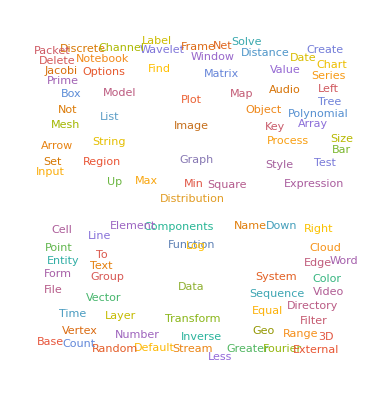

```mathematica
WordCloudFromFunctionData[CanonicalName/@WolframLanguageData[]]
```

Create smaller wordclouds:

```mathematica
frequentWords={"Distribution","Graph","Image","Data","Plot","Find","Geo","List","Matrix","String","Group","Vector","System","Process","Audio","Model","Find","Region","Transform","Number"};
```

Create multiple word clouds

```mathematica
frequentWordCloudMap[word_,options:OptionsPattern[]]:=WordCloudFromFunctionData[Names[StringJoin["*",word,"*"]],options]
```

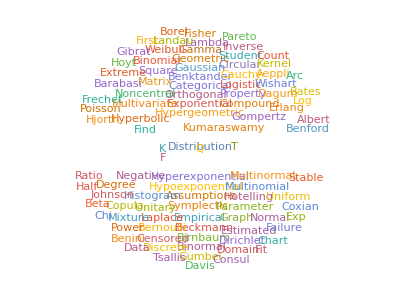

```mathematica
frequentWordCloudMap["Distribution"]
```

Create multiple word clouds

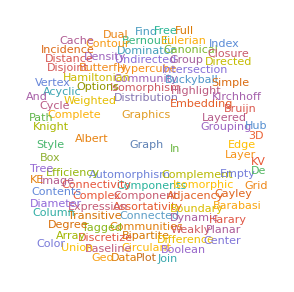
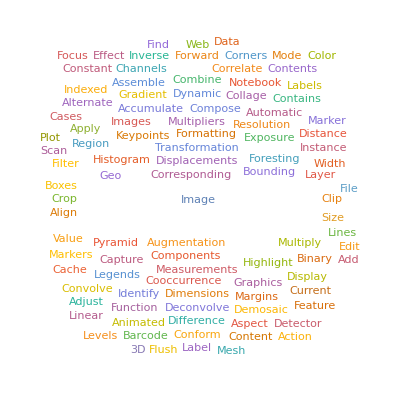
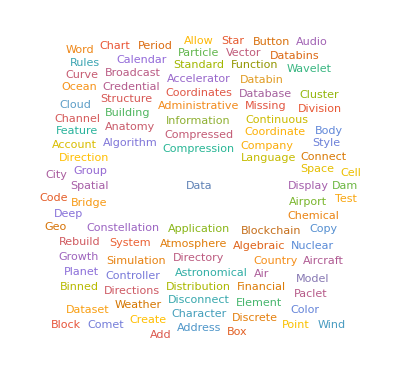
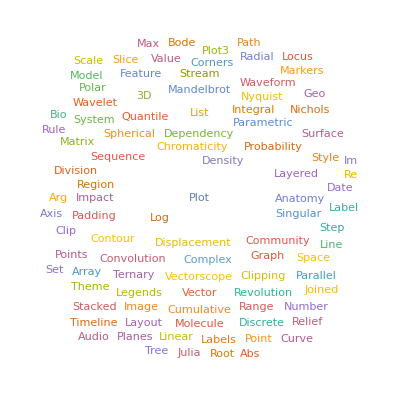
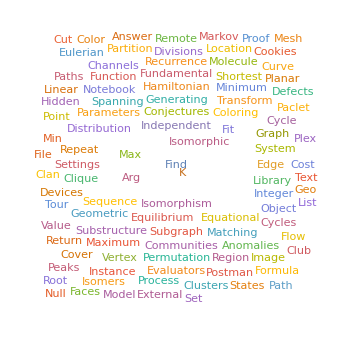
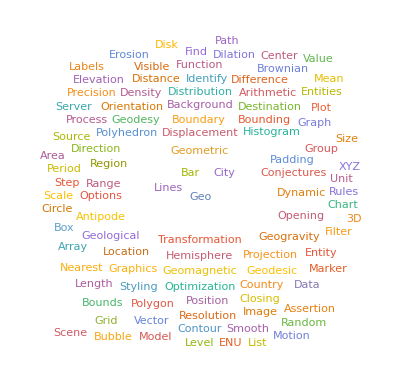
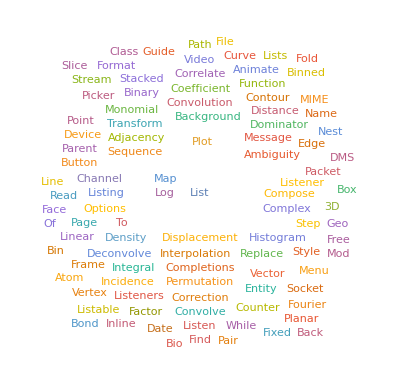
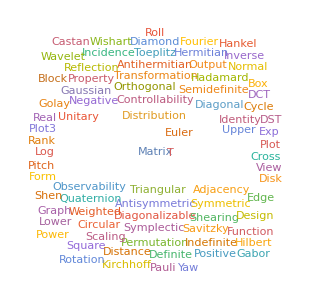
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
frequentWordCloudMap/@frequentWords
```

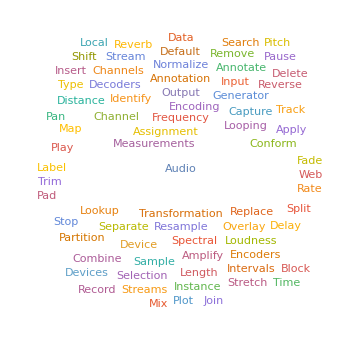
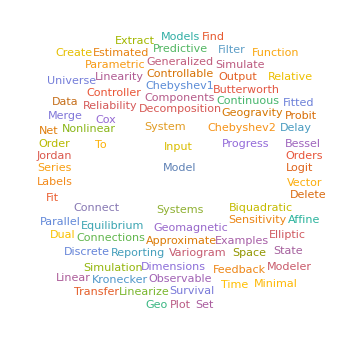
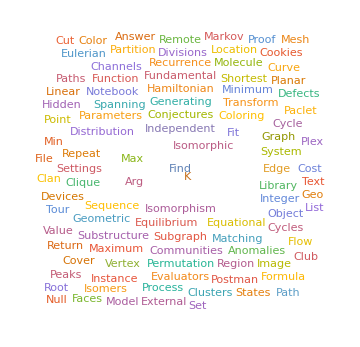
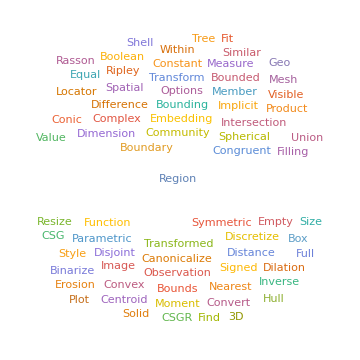
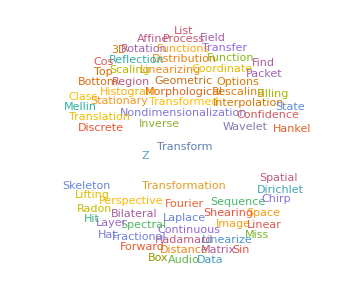
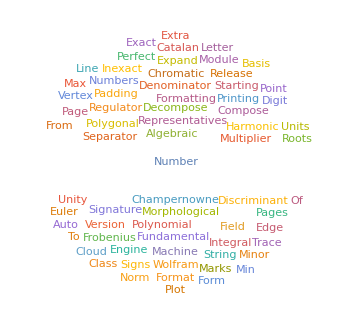

```mathematica
frequentWordCloudMap[#,ImageSize->Medium]&/@frequentWords[[-6;;-1]]
```

Analyze less frequent words

```mathematica
WordCloudFromFunctionData[CanonicalName/@WolframLanguageData[]]
```

-Graphics-

```mathematica
lessFrequentWords={"Packet","Discrete","Channel","Label","Wavelet","Frame","Net","Solve","Distance","Date","Chart","Create","Series","Left","Tree","Delete","Notebook","Jacobi","Options","Prime","Map","Polynomial","Input","Up","Square","Expression","Element","Word","Directory","Range","Base","Count","Random","Fourier","External"};
```

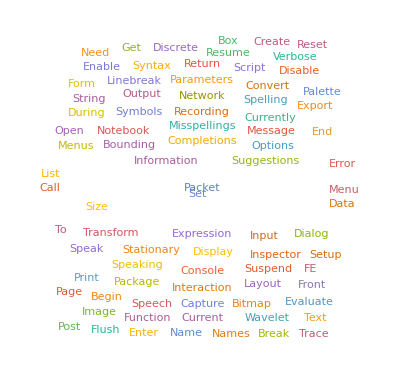
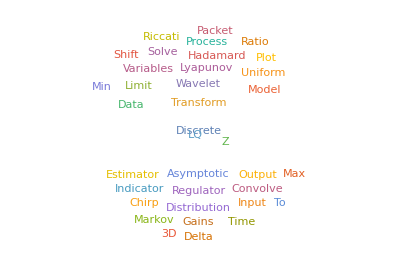
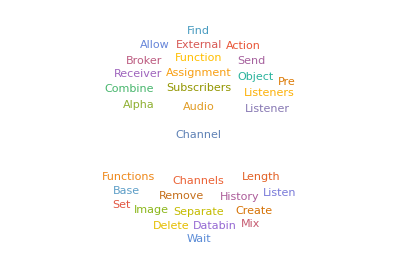
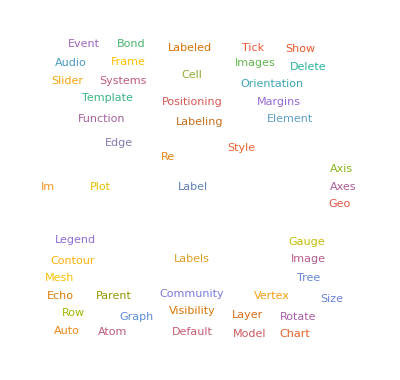
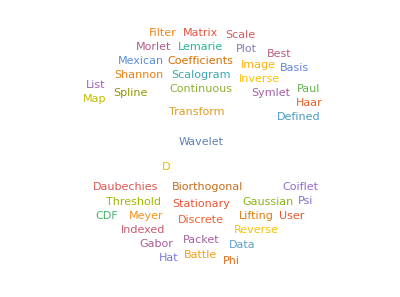
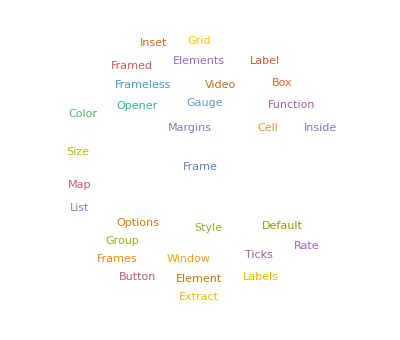
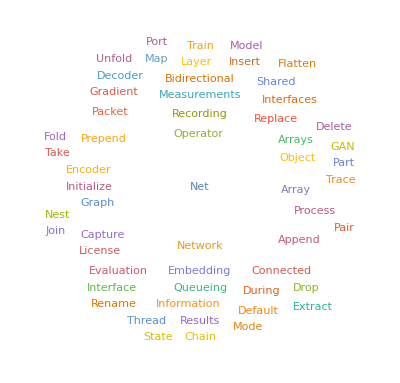
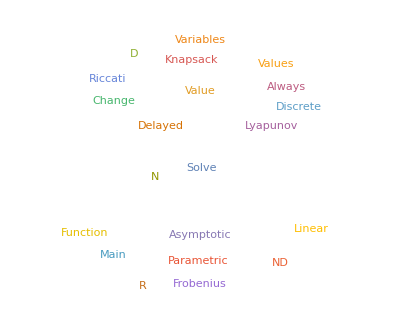

```mathematica
frequentWordCloudMap/@lessFrequentWords
```

```mathematica
WolframLanguageData["Graph","RelationshipCommunityGraph"]
```

-Graphics-

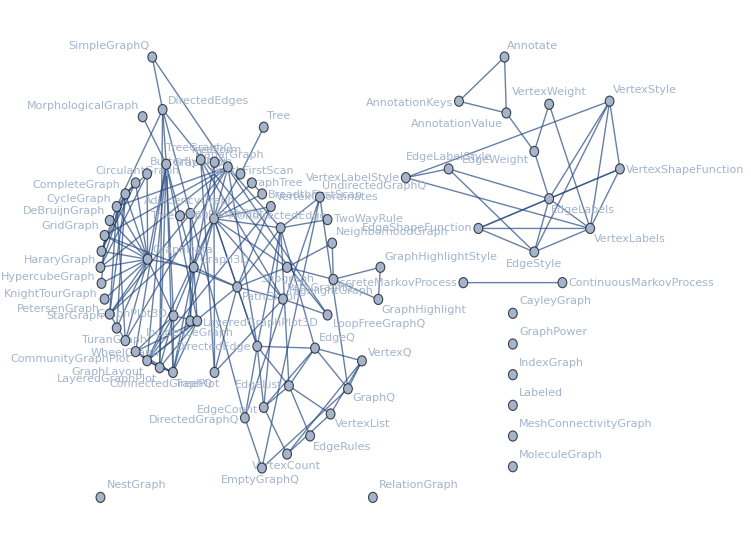

```mathematica
WolframLanguageData["Graph","RelationshipGraph"]
```

## Analyzing Graphs

```mathematica
Select[StringContainsQ[#,"Graph"|"graph"]&][names]
```

{$CryptographicEllipticCurveNames,AcyclicGraphQ,AdjacencyGraph,BarabasiAlbertGraphDistribution,BernoulliGraphDistribution,BipartiteGraphQ,BooleanGraph,BoundaryDiscretizeGraphics,ButterflyGraph,CanonicalGraph,CayleyGraph,CirculantGraph,CommunityGraphPlot,CompleteGraph,CompleteGraphQ,ConnectedGraphComponents,ConnectedGraphQ,CycleGraph,DeBruijnGraph,DegreeGraphDistribution,DirectedGraph,DirectedGraphQ,DiscretizeGraphics,DominatorTreeGraph,DualPlanarGraph,DynamicGeoGraphics,EdgeTaggedGraph,EdgeTaggedGraphQ,EdgeTransitiveGraphQ,EdgeWeightedGraphQ,EmptyGraphQ,EulerianGraphQ,ExpressionGraph,FindGraphCommunities,FindGraphIsomorphism,FindGraphPartition,FindIsomorphicSubgraph,FindSubgraphIsomorphism,FullGraphics,GeoGraphPlot,GeoGraphValuePlot,GeoGraphics,Graph,Graph3D,GraphAssortativity,GraphAutomorphismGroup,GraphCenter,GraphComplement,GraphData,GraphDensity,GraphDiameter,GraphDifference,GraphDisjointUnion,GraphDistance,GraphDistanceMatrix,GraphEmbedding,GraphHighlight,GraphHighlightStyle,GraphHub,GraphIntersection,GraphLayerStyle,GraphLayers,GraphLayout,GraphLinkEfficiency,GraphPeriphery,GraphPlot,GraphPlot3D,GraphPower,GraphPropertyDistribution,GraphQ,GraphRadius,GraphReciprocity,GraphTree,GraphUnion,Graphics,Graphics3D,GraphicsColumn,GraphicsComplex,GraphicsGrid,GraphicsGroup,GraphicsRow,GridGraph,HamiltonianGraphQ,HararyGraph,HighlightGraph,HypercubeGraph,ImageGraphics,IncidenceGraph,IndexEdgeTaggedGraph,IndexGraph,IsomorphicGraphQ,IsomorphicSubgraphQ,KEdgeConnectedGraphQ,KVertexConnectedGraphQ,KirchhoffGraph,KnightTourGraph,LayeredGraphPlot,LayeredGraphPlot3D,LexicographicOrder,LexicographicSort,LineGraph,LoopFreeGraphQ,MeanGraphDistance,MeshConnectivityGraph,MixedGraphQ,MoleculeGraph,MorphologicalGraph,MultigraphQ,NearestNeighborGraph,NeighborhoodGraph,NestGraph,NetGraph,ParagraphIndent,ParagraphSpacing,PathGraph,PathGraphQ,PetersenGraph,PlanarGraph,PlanarGraphQ,PriceGraphDistribution,RandomGraph,RelationGraph,ReverseGraph,SimpleGraph,SimpleGraphQ,SpatialGraphDistribution,StarGraph,Subgraph,TelegraphProcess,TransitiveClosureGraph,TransitiveReductionGraph,TreeGraph,TreeGraphQ,TuranGraph,UndirectedGraph,UndirectedGraphQ,UniformGraphDistribution,VertexInComponentGraph,VertexOutComponentGraph,VertexTransitiveGraphQ,VertexWeightedGraphQ,WattsStrogatzGraphDistribution,WeaklyConnectedGraphComponents,WeaklyConnectedGraphQ,WeightedAdjacencyGraph,WeightedGraphQ,WheelGraph}

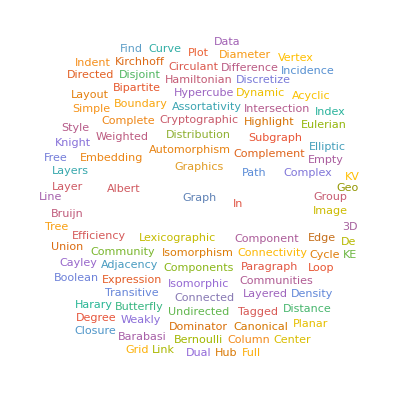

```mathematica
WordCloudFromFunctionData[Select[StringContainsQ[#,"Graph"|"graph"]&][names]]
```

## Matrix

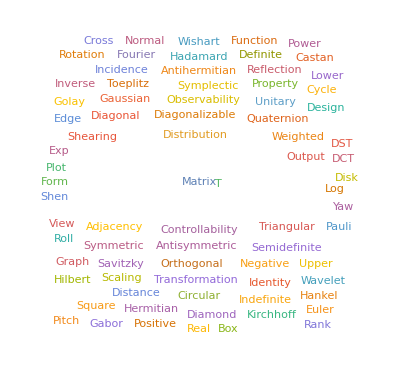

```mathematica
WordCloudFromFunctionData[Select[StringContainsQ[#,"Matrix"]&][names]]
```

## Symmetric

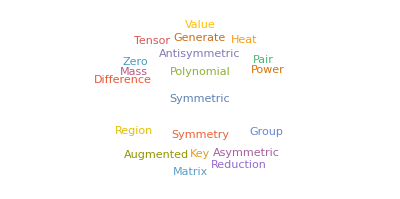

```mathematica
WordCloudFromFunctionData[Select[StringContainsQ[#,"Symmetric"|"symmetric"|"symmetry"|"Symmetry"]&][names]]
```

```mathematica
SymmetricDifference[({{a, b, c}, {b, c, e}, {d, f, g}}),Transpose[({{a, b, c}, {b, c, e}, {d, f, g}})]]
```

{{a,b,c},{a,b,d},{b,c,e},{b,c,f},{c,e,g},{d,f,g}}